```mathematica
(*By Riccardo Marrocchio
rmarrocchio@stanford.edu
January 27th 2024*)

Remove["Global`*"]

(*Parameters of the model*)

kA=146.3; (*anchor stiffness [fN.nm-1]*)
lA=6.6*10^(-4); (*damping coefficient of the anchors [fN.s.nm-1]*)
kL=562; (*link stiffness [fN.nm-1]*)
lL=3.6*10^(-3); (*damping coefficient of the links [fN.nm-1]*)
kbT=4061.9;(*Boltzmann constant times temperature [fN.nm]. Temperature 294.2 K (room temperature)*)

(*function to derive n,m component of susceptibility matrix as a function of a=kA+I*lA and b=kL+I*lL Eq.14*)
cc1[n_,a_,b_]=2^(-1-n) ((a+2 b-√a √(a+4 b))^n+(a+2 b+√a √(a+4 b))^n+(√a (-(a+2 b-√a √(a+4 b))^n+(a+2 b+√a √(a+4 b))^n))/(√(a+4 b)));
chic2[nst_,n1_,n2_,a_,b_]:=FullSimplify[cc1[nst-Max[n2,n1]-1-IntegerPart[(nst-1)/2],a,b]*cc1[Min[n1,n2]+IntegerPart[(nst-1)/2],a,b]*b^Abs[(n2-n1)]/(cc1[nst,a,b]-b*cc1[nst-1,a,b])];

(*function to derive n,m component of power spectrum Eq.17*)
  PSDc2[nst_,n_,m_] := 
 Module[{chinm,psdnm,a3,b3}, 
  chinm=Apart[chic2[nst,n,m,a3,b3]];
  a3=kA1+I*w*lA1;
  b3=kL1+I*w*lL1;
  psdnm=-4*kbT*Im[chinm]/w;
  psdnm];

(*function to derive coherency between stereocilia n,m Eq.18*) 
coherc2[nst_,n_,m_] := 
 Module[{cohernm,psdnm,psdnn,psdmm,a3,b3}, 
  psdnm=PSDc2[nst,n,m];
  psdnn=PSDc2[nst,n,n];
  psdmm=PSDc2[nst,m,m];
  cohernm=psdnm/Sqrt[psdnn*psdmm];
  cohernm];

(*PLOT SETTINGS*)
  
TickLength = 0.02;
Xmin = 0;
Xmax = 10 - 1;
Ymin = 0;
Ymax=20;
deltaY=2;
plotrangepsd={{10^(2),10^6},{0.5*10^(-7),10^(-2)}};
plotrangecoher={{10^(2),10^6},{-1.05,1.05}};
framelabels={{"power spectrum (\!\(\*SuperscriptBox[\(nm\), \(2\)]\)/Hz)",None},{"noise frequency (Hz)",None}};
TickLength1=0.03;
Yticks1=Table[{10^k, Superscript[10,k], {0, TickLength1}}, {k, -10, 1,1}];
TickLength2=0.02;
aa=Table[0,{20},{4}];
For[k=1,k<=20,k++,
aa[[k]]=Table[{l*10^-(-k+11),, {0, TickLength2}}, {l, 2, 8,2}];
]
YTicks=Union[Yticks1,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];

Xticks1=Table[{10^k, Superscript[10,k], {0, TickLength1}}, {k, 0, 6,1}];(*Table[{i, i, {0, TickLength}}, {i, Xmin, Xmax, 1}];*)
XTicks=Union[Xticks1,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];

pady=80;
padx=70;
pad2=30;
fntsize=18;

frameticksy={{{1/100000,Superscript[10,-5],{0,0.03}},{1/10000,Superscript[10,-4],{0,0.03}},{1/1000,Superscript[10,-3],{0,0.03}},{1/100,Superscript[10,-2],{0,0.03}}},None};
frameticksyENLAR={{{1/100000,Superscript[10,-5],{0,0.03}},{1/10000,Superscript[10,-4],{0,0.03}},{1/1000,Superscript[10,-3],{0,0.03}},{2*10^-5,,{0,0.02}},{4*10^-5,,{0,0.02}},{6*10^-5,,{0,0.02}},{8*10^-5,,{0,0.02}},{2*10^-4,,{0,0.02}},{4*10^-4,,{0,0.02}},{6*10^-4,,{0,0.02}},{8*10^-4,,{0,0.02}}},None};
frameticksx={{{1000,Superscript[10,3],{0,0.03}},{10000,Superscript[10,4],{0,0.03}},{100000,Superscript[10,5],{0,0.03}},{2*10^3,,{0,0.02}},{4*10^3,,{0,0.02}},{6*10^3,,{0,0.02}},{8*10^3,,{0,0.02}},{2*10^4,,{0,0.02}},{4*10^4,,{0,0.02}},{6*10^4,,{0,0.02}},{8*10^4,,{0,0.02}}},None};
frameticksycoher={{{0,0,{0,0.03}},{0.2,0.2,{0,0.03}},{0.4,0.4,{0,0.03}},{0.6,0.6,{0,0.03}},{0.8,0.8,{0,0.03}},{1.0,"1.0",{0,0.03}}}, None};
frameticksycoherneg={{{0,0,{0,0.03}},{0.5,0.5,{0,0.03}},{1.0,"1.0",{0,0.03}},{-0.5,-0.5,{0,0.03}},{-1.0,"-1.0",{0,0.03}},{-1.5,"-1.5",{0,0.03}}}, None};

fntsize=18;

xmin=2.5*10^2; (*physiological frequency range*)
xmax=7*10^3; (*physiological frequency range*)
ymin=10^(-10);
ymax=10^(10);
ymincoher=-2;
ymaxcoher=2;
dl1 = {{xmin,ymin},{xmax,ymin}};
dl2 = {{xmin,ymax},{xmax,ymax}};
dl1coher = {{xmin,ymincoher},{xmax,ymincoher}};
dl2coher = {{xmin,ymaxcoher},{xmax,ymaxcoher}};
```

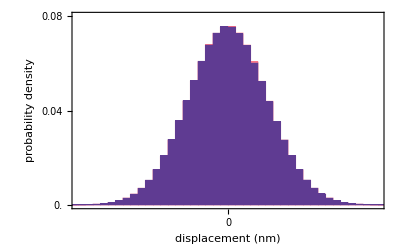

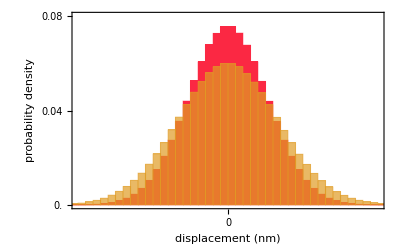

```mathematica
(*Fig 1 plots of probability density of stereocilium 0,1 and 8*)

(*parameters of simulation*)

totallength=1; (*total length of simulation[s]*)
deltatsima=0.000001/(10); (*time step stimulation [s]*)

(*intensity of noise forces*)
g0=2*kbT (lA+lL); 
g1=2*kbT (lA+2lL);
g2=2*kbT (lA+lL);

(*derivation of matrix of correlations between noise forces*)
Ch[nst_]:=DiagonalMatrix[Table[1,nst]]+DiagonalMatrix[Table[rho2,nst-1],1]+DiagonalMatrix[Table[rho2,nst-1],-1];
Mc=Ch[16];
Mc[[1,2]]=rho1;
Mc[[2,1]]=rho1;
Mc[[16-1,16]]=rho1;
Mc[[16,16-1]]=rho1;
rho1=-lL/Sqrt[(lL+lA)(lA+2lL)];
rho2=-lL/(lA+2lL);

Chd=CholeskyDecomposition[Mc]†;

(*derivation of langevin equations*)

xc[n_]:=Symbol["x" <> ToString[n]]
wc[n_]:=Symbol["w" <> ToString[n]]

laneq0[nst_]:=(lA+lL)*ⅆx0[t] == (-kA*x0[t]- kL*(x0[t]-x1[t]))*ⅆt+lL*ⅆx1[t] +Sqrt[g0]*(Total[Table[Chd[[1,j]]*ⅆwc[j][t],{j,1,nst}]]);
laneq[n_,nst_]:=(lA+2*lL)*ⅆxc[n][t] == (-kA*xc[n][t]- kL*(xc[n][t]
-xc[n-1][t])-kL*(xc[n][t]-xc[n+1][t]))*ⅆt +lL*ⅆxc[n-1][t]+lL*ⅆxc[n+1][t] + Sqrt[g1]*(Total[Table[Chd[[n+1,j]]*ⅆwc[j][t],{j,1,nst}]])
laneqlast[nst_]:=(lA+lL)*ⅆxc[nst-1][t] == (-kA*xc[nst-1][t]- kL*(xc[nst-1][t]-xc[nst-2][t]))*ⅆt+lL*ⅆxc[nst-2][t]+Sqrt[g2]*(Total[Table[Chd[[nst,j]]*ⅆwc[j][t],{j,1,nst}]])

laninteqsa=Table[laneq[n,16],{n,1,16-2}];
laninteqsb=Prepend[laninteqsa,laneq0[16]];
laninteqs=Append[laninteqsb,laneqlast[16]];
variabl=Table[xc[n][t],{n,0,16-1}];
initialvar=Table[xc[n],{n,0,16-1}];
initialcond=Table[0,{n,0,16-1}];
wieners=Table[wc[n]\[Distributed] WienerProcess[],{n,1,16}];

(*derivation of time series*)
proc=ItoProcess[laninteqs,variabl,{initialvar,initialcond},t,wieners];
  ap= RandomFunction[proc, {0., totallength,deltatsima}];

(*plot settings*)
Ytickshist2=Table[{k, k, {0, TickLength1}}, {k, 0.00, 0.20,0.02}];
Xticks11=Table[{k, k, {0, TickLength1}}, {k, -40, 40,5}];

(*plots*)
Histogram[{ap["PathComponent",8]["Values"],ap["PathComponent",9]["Values"]},{0.5},"Probability", PlotRange->{{-10,10},{0,0.08}},LabelStyle->{FontSize->18},ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{Ytickshist2, None}, {Xticks11, None}},FrameLabel->{"displacement (nm)", "probability density"},ChartStyle->{RGBColor[251/255, 40/255, 67/255],Opacity[1,RGBColor[95/255, 59/255, 146/255]]}]
Histogram[{ap["PathComponent",8]["Values"],ap["PathComponent",16]["Values"]},{0.5},"Probability",PlotRange->{{-10,10},{0,0.08}},LabelStyle->{FontSize->18},ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{Ytickshist2, None}, {Xticks11, None}},FrameLabel->{"displacement (nm)", "probability density"},ChartStyle->{Opacity[1,RGBColor[251/255, 40/255, 67/255]],Opacity[.70,RGBColor[225/255, 156/255, 36/255]]}]
```

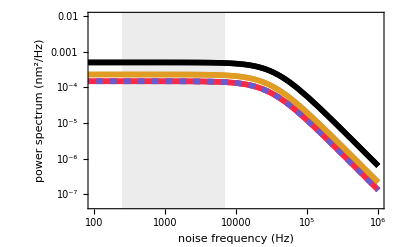

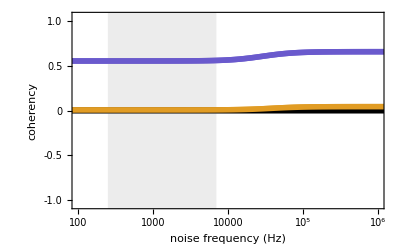

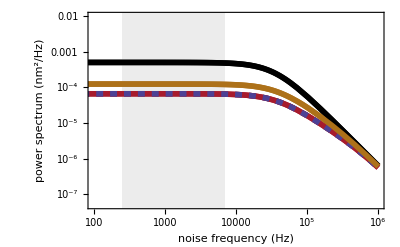

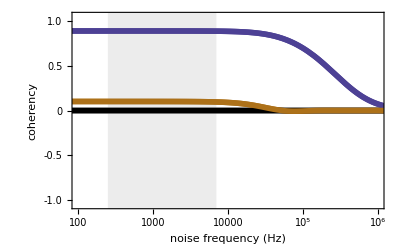

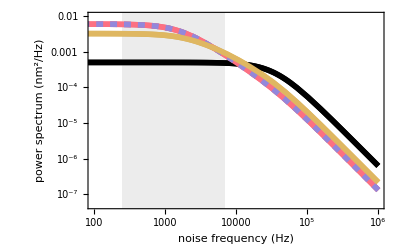

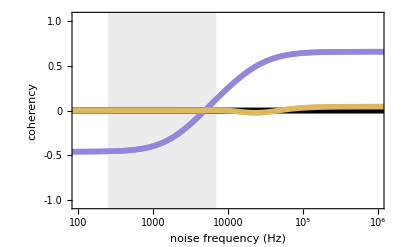

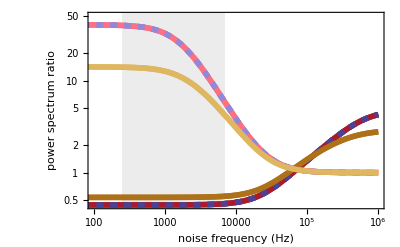

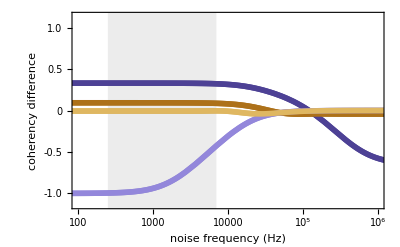

```mathematica
(*Fig 2A & 3A plots of power spectrum and coherency vs noise frequency in the case of stereocilia coupled by both links*)

(*Fig 2A & 3A plots of power spectrum and coherency vs noise frequency in the case of stereocilia coupled by both links*)

(*plot settings*)
plotstylecoh={{Thickness->0.01,RGBColor[0*251/255, 0*41/255, 0*67/255]},{Thickness->0.01,RGBColor[106/255, 90/255, 205/255]},{Thickness->0.01,RGBColor[225/255, 156/255, 36/255]}};
plotstylepsd={{Thickness->0.01,RGBColor[0*145/255, 0*145/255, 0*145/255]},{Thickness->0.01,RGBColor[251/255, 41/255, 67/255]},{Thickness->0.01,RGBColor[106/255, 90/255, 205/255],Dashed},{Thickness->0.01,RGBColor[225/255, 156/255, 36/255]}};

(*derivation of power spectra and coherency*)
psd00=PSDc2[16,0,0];
psd11=PSDc2[16,1,1];
psd88=PSDc2[16,8,8];

coher01=coherc2[16,0,1];
coher08=coherc2[16,0,8];

(*plots*)
LogLogPlot[{psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL},psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},psd11/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}},{f,0.01,10^6},
PlotRange->plotrangepsd,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylepsd, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{YTicks, None}, {XTicks, None}},FrameLabel->framelabels,GridLines -> {{5000}, {}},GridLinesStyle->Directive[RGBColor[0,125/255,128/255],Dashed,Thickness->0.01]];
Show[%,ListLogLogPlot[{dl1, dl2}, Joined -> True, 
  PlotRange -> {Automatic, Automatic}, GridLines -> None, 
  PlotStyle -> {White, White}, Filling -> {1 -> {2}}, 
  FillingStyle -> Directive[Opacity[0.15], Gray], ImageSize -> 540]];
Show[%,LogLogPlot[{psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL},psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},psd11/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}},{f,0.01,10^6},PlotRange->plotrangepsd,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylepsd, Background->White . Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{YTicks, None}, {XTicks, None}},FrameLabel->framelabels]
]

LogLinearPlot[{coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL},coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}},{f,1,10^7},PlotRange->plotrangecoher,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicks,None}},FrameLabel->{"noise frequency (Hz)", "coherency"},GridLines -> {{5000}, {}},GridLinesStyle->Directive[RGBColor[0,125/255,128/255],Dashed,Thickness->0.01]];
Show[%,ListLogLogPlot[{dl1, dl2}, Joined -> True, 
  PlotRange -> {Automatic, Automatic}, GridLines -> None, 
  PlotStyle -> {White, White}, Filling -> {1 -> {2}}, 
  FillingStyle -> Directive[Opacity[0.15], Gray], ImageSize -> 540]];
Show[%,LogLinearPlot[{coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL},coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}},{f,1,10^7},PlotRange->plotrangecoher,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicks,None}},FrameLabel->{"noise frequency (Hz)", "coherency"}]
]

(*Fig2B & 3B PLOT plots of power spectrum and coherency vs noise frequency in the case of stereocilia coupled only by stiff links*)

(*plot settings*)
(*plot settings*)
plotstylecoh={{Thickness->0.01,RGBColor[0*145/255, 0*145/255, 0*145/255]},{Thickness->0.01,RGBColor[77/255, 65/255, 149/255]},{Thickness->0.01,RGBColor[173/255, 113/255, 25/255]}};
plotstylepsd={{Thickness->0.01,RGBColor[0*145/255, 0*145/255, 0*145/255]},{Thickness->0.01,Darker[RGBColor[251/255, 41/255, 67/255]]},{Thickness->0.01,RGBColor[77/255, 65/255, 149/255],Dashed},{Thickness->0.01,RGBColor[173/255, 113/255, 25/255]}};

(*plots*)
LogLogPlot[{psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL},psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL},psd11/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL},psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL}},{f,0.01,10^6},PlotRange->plotrangepsd,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylepsd, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{YTicks, None}, {XTicks, None}},FrameLabel->framelabels,GridLines -> {{5000}, {}},GridLinesStyle->Directive[RGBColor[0,125/255,128/255],Dashed,Thickness->0.01]];
Show[%,ListLogLogPlot[{dl1, dl2}, Joined -> True, 
  PlotRange -> {Automatic, Automatic}, GridLines -> None, 
  PlotStyle -> {White, White}, Filling -> {1 -> {2}}, 
  FillingStyle -> Directive[Opacity[0.15], Gray], ImageSize -> 540]];
Show[%,LogLogPlot[{psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL},psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL},psd11/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL},psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL}},{f,0.01,10^6},PlotRange->plotrangepsd,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylepsd, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{YTicks, None}, {XTicks, None}},FrameLabel->framelabels]]

LogLinearPlot[{coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL},coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL},coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL}},{f,1,10^7},PlotRange->plotrangecoher,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicks,None}},FrameLabel->{"noise frequency (Hz)", "coherency"},GridLines -> {{5000}, {}},GridLinesStyle->Directive[RGBColor[0,125/255,128/255],Dashed,Thickness->0.01]];
Show[%,ListLogLogPlot[{dl1, dl2}, Joined -> True, 
  PlotRange -> {Automatic, Automatic}, GridLines -> None, 
  PlotStyle -> {White, White}, Filling -> {1 -> {2}}, 
  FillingStyle -> Directive[Opacity[0.15], Gray], ImageSize -> 540]];
Show[%,LogLinearPlot[{coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL},coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL},coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL}},{f,1,10^7},PlotRange->plotrangecoher,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicks,None}},FrameLabel->{"noise frequency (Hz)", "coherency"}]]

(*Fig2C & 3 C plots of power spectra and coherency vs noise frequency in the case of stereocilia coupled only by damped links*)

(*plot settings*)
plotstylecoh={{Thickness->0.01,RGBColor[0*145/255, 0*145/255, 0*145/255]},{Thickness->0.01,RGBColor[147/255, 135/255, 219/255]},{Thickness->0.01,RGBColor[223/255, 183/255, 97/255]}};
plotstylepsd={{Thickness->0.01,RGBColor[0*145/255, 0*145/255, 0*145/255]},{Thickness->0.01,Lighter[RGBColor[251/255, 41/255, 67/255]]},{Thickness->0.01,RGBColor[147/255, 135/255, 219/255],Dashed},{Thickness->0.01,RGBColor[223/255, 183/255, 97/255]}};

(*plots*)
LogLogPlot[{psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL},psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL},psd11/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL},psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL}},{f,0.01,10^6},PlotRange->plotrangepsd,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylepsd, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{YTicks, None}, {XTicks, None}},FrameLabel->framelabels,GridLines -> {{5000}, {}},GridLinesStyle->Directive[RGBColor[0,125/255,128/255],Dashed,Thickness->0.01]];(*,GridLines -> {{5000}, {}},GridLinesStyle->Directive[Black,Dashed,Thickness->0.01]*)
Show[%,ListLogLogPlot[{dl1, dl2}, Joined -> True, 
  PlotRange -> {Automatic, Automatic}, GridLines -> None, 
  PlotStyle -> {White, White}, Filling -> {1 -> {2}}, 
  FillingStyle -> Directive[Opacity[0.15], Gray], ImageSize -> 540]];
 Show[%,LogLogPlot[{psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL},psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL},psd11/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL},psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL}},{f,0.01,10^6},PlotRange->plotrangepsd,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylepsd, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{YTicks, None}, {XTicks, None}},FrameLabel->framelabels]]
LogLinearPlot[{coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL},coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL},coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL}},{f,1,10^7},PlotRange->plotrangecoher,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicks,None}},FrameLabel->{"noise frequency (Hz)", "coherency"},GridLines -> {{5000}, {}},GridLinesStyle->Directive[RGBColor[0,125/255,128/255],Dashed,Thickness->0.01]];
Show[%,ListLogLogPlot[{dl1, dl2}, Joined -> True, 
  PlotRange -> {Automatic, Automatic}, GridLines -> None, 
  PlotStyle -> {White, White}, Filling -> {1 -> {2}}, 
  FillingStyle -> Directive[Opacity[0.15], Gray], ImageSize -> 540]];
 Show[%,LogLinearPlot[{coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL},coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL},coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL}},{f,1,10^7},PlotRange->plotrangecoher,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicks,None}},FrameLabel->{"noise frequency (Hz)", "coherency"}]
] 

(*Fig2D & 3 D plots of power spectrum ratio and coherency differences*)

(*plot settings*)
plotrangeratios={{10^(2),10^6},{0,50}};

YTicksratios1=Table[{k, k, {0, TickLength1}}, {k, 0, 50,10}];
bb=Table[0,{20},{4}];
For[k=1,k<=20,k++,
bb[[k]]=Table[{l,, {0, TickLength2}}, {l, 5, 55,10}];
]
YTicksratios=Union[YTicksratios1,bb[[1]],bb[[2]],bb[[3]],bb[[4]],bb[[5]],bb[[6]],bb[[7]],bb[[8]],bb[[9]],bb[[10]],bb[[11]],bb[[12]],bb[[13]],bb[[14]],bb[[15]],bb[[16]],bb[[17]],bb[[18]],bb[[19]],bb[[20]]];

plotstyleratios=plotstyleratios={{Thickness->0.01,Darker[RGBColor[251/255, 41/255, 67/255]]},{Thickness->0.01, RGBColor[Rational[77, 255], Rational[13, 51], Rational[149, 255]],Dashed},{Thickness->0.01,RGBColor[Rational[173, 255], Rational[113, 255], Rational[5, 51]]},{Thickness->0.01,Lighter[RGBColor[251/255, 41/255, 67/255]]},{Thickness->0.01,RGBColor[Rational[49, 85], Rational[9, 17], Rational[73, 85]],Dashed},{Thickness->0.01,RGBColor[Rational[223, 255], Rational[61, 85], Rational[97, 255]]}};
framelabelsratios={{"power spectrum ratio",None},{"noise frequency (Hz)",None}};

(*plots*)
LogLogPlot[{(psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL})/(psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}),(psd11/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL})/(psd11/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}),(psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL})/(psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}),(psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL})/psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},(psd11/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL})/(psd11/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}),(psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL})/(psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL})},{f,0.01,10^6},
PlotRange->plotrangeratios,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},
PlotStyle->plotstyleratios, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{XTicks, None}, {XTicks, None}},FrameLabel->framelabelsratios,GridLines -> {{5000}, {}},GridLinesStyle->Directive[RGBColor[0,125/255,128/255],Dashed,Thickness->0.01]];
Show[%,ListLogLogPlot[{dl1, dl2}, Joined -> True, 
  PlotRange -> {Automatic, Automatic}, GridLines -> None, 
  PlotStyle -> {White, White}, Filling -> {1 -> {2}}, 
  FillingStyle -> Directive[Opacity[0.15], Gray], ImageSize -> 540]];
Show[%,LogLogPlot[{(psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL})/(psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}),(psd11/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL})/(psd11/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}),(psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL})/(psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}),(psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL})/psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},(psd11/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL})/(psd11/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}),(psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL})/(psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL})},{f,0.01,10^6},
PlotRange->plotrangeratios,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},
PlotStyle->plotstyleratios, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{XTicks, None}, {XTicks, None}},FrameLabel->framelabelsratios]]

(*plot settings*)
plotstyleratioscoh={{Thickness->0.01,RGBColor[77/255, 65/255, 149/255]},{Thickness->0.01,RGBColor[173/255, 113/255, 25/255]},{Thickness->0.01,RGBColor[147/255, 135/255, 219/255]},{Thickness->0.01,RGBColor[223/255, 183/255, 97/255]}};
plotrangecoherratios={{10^(2),10^6},{-1.15,1.15}};

(*plots*)
LogLinearPlot[{(coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL})-(coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}),(coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL})-(coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}),(coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL})-(coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}),(coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL})-(coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL})},{f,1,10^7},
PlotRange->plotrangecoherratios,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},
PlotStyle->plotstyleratioscoh, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicks,None}},FrameLabel->{"noise frequency (Hz)", "coherency difference"},GridLines -> {{5000}, {}},GridLinesStyle->Directive[RGBColor[0,125/255,128/255],Dashed,Thickness->0.01]];
Show[%,ListLogLogPlot[{dl1, dl2}, Joined -> True, 
  PlotRange -> {Automatic, Automatic}, GridLines -> None, 
  PlotStyle -> {White, White}, Filling -> {1 -> {2}}, 
  FillingStyle -> Directive[Opacity[0.15], Gray], ImageSize -> 540]];
Show[%,LogLinearPlot[{(coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL})-(coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}),(coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL})-(coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}),(coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL})-(coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL}),(coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL})-(coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL})},{f,1,10^7},
Axes->False,PlotRange->plotrangecoher,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},
PlotStyle->plotstyleratioscoh, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicks,None}},FrameLabel->{"noise frequency (Hz)", "coherency difference"}]]
```

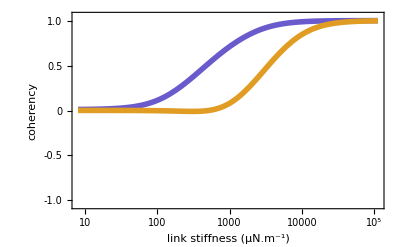

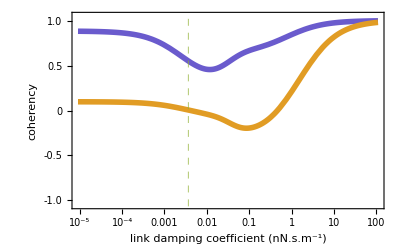

```mathematica
(*Fig 4 plots of coherency between stereocilia 0 and 1 and between 0 and 8 versus link stiffness and link damping coefficient*)

(*derivation of coherency*)
coher01=coherc2[16,0,1];
coher08=coherc2[16,0,8];

(*plot settings*)
col01= RGBColor[106/255,91/255,205/255];
col08= RGBColor[225/255,156/255,36/255];

plotstylecoh01 = {{Thickness->0.01,
   col01}
   }; 
   
   plotstylecoh08 = {{Thickness->0.01,
   col08}
   };

Xticks1a=Table[{10^k, Superscript[10,k], {0, TickLength1}}, {k, -10, 10,1}];
XTicksa=Union[Xticks1a,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];
plotrangecoher1={{562/70,562*200},{-1.05,1.05}};

(*plot*)
LogLinearPlot[coher01/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),lL1->3.646*10^(-3)},
{kL1,562/70,562*200},PlotRange->plotrangecoher1,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh01, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicksa,None}},FrameLabel->{"link stiffness (μN.\!\(\*SuperscriptBox[\(m\), \(-1\)]\))", "coherency"}
,GridLines -> {{562}, {}}, GridLinesStyle->Directive[RGBColor[165/255,97/255,157/255],Dashed,Thickness->0.01]];
Show[%,LogLinearPlot[coher08/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),lL1->3.646*10^(-3)},
{kL1,562/70,562*200},PlotRange->plotrangecoher1,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh08, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicksa,None}},FrameLabel->{"link stiffness (μN.\!\(\*SuperscriptBox[\(m\), \(-1\)]\))", "coherency"}
,GridLines -> {{562}, {}}, GridLinesStyle->Directive[RGBColor[165/255,97/255,157/255],Dashed,Thickness->0.01]]]

(*plot settings*)
Xticks1b=Table[{10^k, Superscript[10,k], {0, TickLength1}}, {k, -9, 16,2}];(*Table[{i, i, {0, TickLength}}, {i, Xmin, Xmax, 1}];*)
Xticks2b=Table[{10^k, , {0, TickLength1}}, {k, -8, 16,2}];(*Table[{i, i, {0, TickLength}}, {i, Xmin, Xmax, 1}];*)
XTicksb=Union[Xticks1b,Xticks2b,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];
plotrangecoher2={{3.646*10^(-3)/400,3.646*10^(-3)*30000},{-1.05,1.05}};

(*plot*)
LogLinearPlot[coher01/.{w->5000*2*Pi,kA1->146.3,kL1->562,lA1->6.563*10^(-4)},
{lL1,3.646*10^(-3)/400,3.646*10^(-3)*30000},PlotRange->plotrangecoher2,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh01, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicksb,None}},FrameLabel->{"link damping coefficient (nN.s.\!\(\*SuperscriptBox[\(m\), \(-1\)]\))", "coherency"}
,GridLines -> {{3.646*10^(-3)}, {}}, GridLinesStyle->Directive[RGBColor[144/255,176/255,50/255],Dashed,Thickness->0.01]];
Show[%,LogLinearPlot[coher08/.{w->5000*2*Pi,kA1->146.3,kL1->562,lA1->6.563*10^(-4)},
{lL1,3.646*10^(-3)/400,3.646*10^(-3)*30000},PlotRange->plotrangecoher2,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh08, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicksb,None}},FrameLabel->{"link damping coefficient (nN.s.\!\(\*SuperscriptBox[\(m\), \(-1\)]\))", "coherency"}
,GridLines -> {{3.646*10^(-3)}, {}}, GridLinesStyle->Directive[RGBColor[144/255,176/255,50/255],Dashed,Thickness->0.01]]]
```

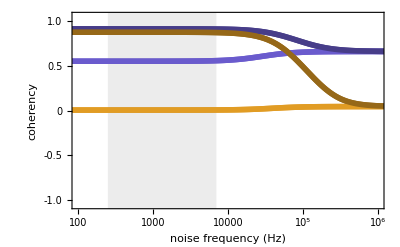

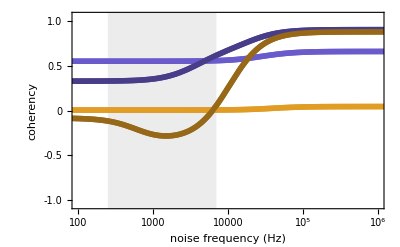

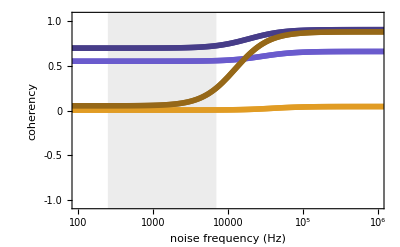

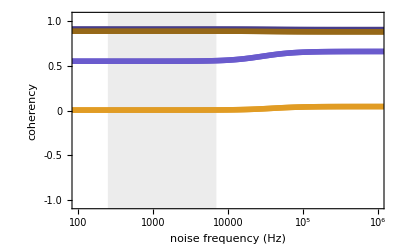

```mathematica
(*Fig 5 of coherency between 0 and 1 and 0 and 8 for different strengths of the links*)

(*derivation of coherency*)
coher01=coherc2[16,0,1];
coher08=coherc2[16,0,8];

(*plot settings*)
col01= RGBColor[106/255,91/255,205/255];
col08= RGBColor[225/255,156/255,36/255];
plotstylecoh01 = {{Thickness->0.01,
   col01},
   {Thickness->0.01,Darker[col01]}
   ,{Thickness->0.01,
   col08},
   {Thickness->0.01,Darker[col08]}
   }; 

(*plot*)
pl1=LogLinearPlot[{coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->5*kL,lL1->lL},coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->20*kL,lL1->lL}}
,{f,1,10^7},PlotRange->plotrangecoher,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh01, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicks,None}},FrameLabel->{"noise frequency (Hz)", "coherency"},GridLines -> {{5000}, {}},GridLinesStyle->Directive[RGBColor[0,125/255,128/255],Dashed,Thickness->0.01]];
Show[%,ListLogLogPlot[{dl1, dl2}, Joined -> True, 
  PlotRange -> {Automatic, Automatic}, GridLines -> None, 
  PlotStyle -> {White, White}, Filling -> {1 -> {2}}, 
  FillingStyle -> Directive[Opacity[0.15], Gray], ImageSize -> 540]];
 Show[%,pl1]
 

(*plot*)
pl1=LogLinearPlot[{coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->10*lL},coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->80*lL}}
,{f,1,10^7},PlotRange->plotrangecoher,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh01, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicks,None}},FrameLabel->{"noise frequency (Hz)", "coherency"}
,GridLines -> {{5000}, {}},GridLinesStyle->Directive[RGBColor[0,125/255,128/255],Dashed,Thickness->0.01]];

Show[%,ListLogLogPlot[{dl1, dl2}, Joined -> True, 
  PlotRange -> {Automatic, Automatic}, GridLines -> None, 
  PlotStyle -> {White, White}, Filling -> {1 -> {2}}, 
  FillingStyle -> Directive[Opacity[0.15], Gray], ImageSize -> 540]];
 Show[%,pl1]
 
 (*plot*)
 pl1=LogLinearPlot[{coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->5*kL,lL1->10*lL},coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->20*kL,lL1->80*lL}}
,{f,1,10^7},PlotRange->plotrangecoher,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh01, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicks,None}},FrameLabel->{"noise frequency (Hz)", "coherency"}
,GridLines -> {{5000}, {}},GridLinesStyle->Directive[RGBColor[0,125/255,128/255],Dashed,Thickness->0.01]];
Show[%,ListLogLogPlot[{dl1, dl2}, Joined -> True, 
  PlotRange -> {Automatic, Automatic}, GridLines -> None, 
  PlotStyle -> {White, White}, Filling -> {1 -> {2}}, 
  FillingStyle -> Directive[Opacity[0.15], Gray], ImageSize -> 540]];
Show[%,pl1]

(*plot*)
pl1=LogLinearPlot[{coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},coher01/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->15*kL,lL1->10*lL},coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},coher08/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->120*kL,lL1->80*lL}}
,{f,1,10^7},PlotRange->plotrangecoher,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh01, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicks,None}},FrameLabel->{"noise frequency (Hz)", "coherency"}
,GridLines -> {{5000}, {}},GridLinesStyle->Directive[RGBColor[0,125/255,128/255],Dashed,Thickness->0.01]];
Show[%,ListLogLogPlot[{dl1, dl2}, Joined -> True, 
  PlotRange -> {Automatic, Automatic}, GridLines -> None, 
  PlotStyle -> {White, White}, Filling -> {1 -> {2}}, 
  FillingStyle -> Directive[Opacity[0.15], Gray], ImageSize -> 540]];
Show[%,pl1]
```

{RGBColor[0.4375, 0., 0.4375],RGBColor[0.625, 0., 0.625],RGBColor[0.8125, 0., 0.8125],RGBColor[1., 0., 1.],RGBColor[1., 0.15625, 1.],RGBColor[1., 0.3125, 1.],RGBColor[1., 0.46875, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.]}

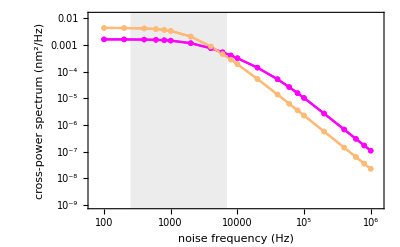

8

8

0

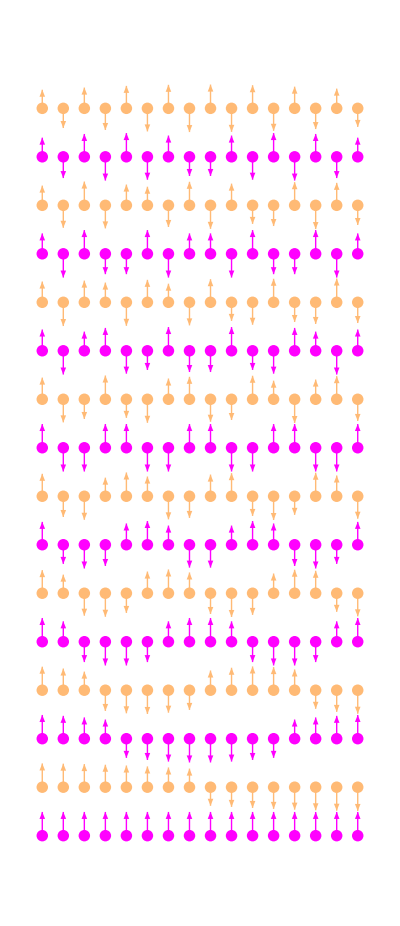

```mathematica
(*Fig.6B-D plots of positive and negative component of power spectrum vs noise frequency*)

(*Calculate power spectral density matrix*)

(*pmat=Table[PSDc[16,x,y]/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lL},{x,0,16-1},{y,0,16-1}]; (*default case with both links*)
pmat=Table[PSDc[16,x,y]/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL},{x,0,16-1},{y,0,16-1}]; (*case only stiff links*)*)
pmat=Table[PSDc2[16,x,y]/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL},{x,-7,8},{y,-7,8}]; (*case only damped links*)

(*Define vector of frequencies over which to calculate eigenvalues*)
f1={10^2,2*10^2,4*10^2,6*10^2,8*10^2,10^3,2*10^3,4*10^3,6*10^3,8*10^3,10^4,2*10^4,4*10^4,6*10^4,8*10^4,10^5,2*10^5,4*10^5,6*10^5,8*10^5,1*10^6};

(*Define vectors for eigenvectors and eigenvalues*)
eigenvandmor=Table[0,{Length[f1]},{1}];
eigenvandm=Table[0,{Length[f1]},{1}];

For[kk=1,kk<=Length[f1],kk++,

(*derive eigensepctrum*)
{vals,vecs} = Eigensystem[{pmat/.{f->f1[[kk]]}, IdentityMatrix[16]}];
{vals,vecs} = Eigensystem[{pmat/.{f->f1[[kk]]}, IdentityMatrix[16]}];

(*order eigenvectors based on the number of neighboring components that are opposite in sign*)
For [jj=1,jj<=Length[vecs],jj++,
If[vecs[[jj]][[1]]<0, vecs[[jj]]=-vecs[[jj]]]; (*change sign of all vectors components so that leftmost stereocilium is >0*)
];
eigenvandm={vals,N[Round[vecs,10^-3]]};
list=eigenvandm[[All]][[2]];
order=Total[Abs[Differences[Sign[Transpose[list]]]]]/2 + Boole[Sign[First[Transpose[list]]] != Sign[Last[Transpose[list]]]];
list=list[[Transpose[order]]];
temp1=Join[eigenvandm[[All]],{Transpose[order]}];
temp2=ReverseSortBy[temp1ᵀ, Last]ᵀ;
eigenvandmor[[kk]]={f1[[kk]],Drop[temp2,-1,0]};
]

(*define general expression of power spectral matrix matrix in terms of eigenvectors and eigenvalues*)
eigenvalues[n_Integer, m_Integer] := 
 Table[Subscript[l, j], {i, n}, {j, m}] //. {x_List} :> x 
 
eigenvectors[n_Integer, m_Integer] := 
 Table[Subscript[u, i, j], {i, n}, {j, m}]//. {x_List} :> x

eigenvmatrix[n_Integer, m_Integer] := 
 Table[Subscript[v, i, j], {i, n}, {j, m}] //. {x_List} :> x

mateigenva=DiagonalMatrix[eigenvalues[1, 16]];
mateigenve=Transpose[eigenvmatrix[16, 16]];
matcov=mateigenve . mateigenva . Transpose[mateigenve];

(*separate positive and negative contribution of coherency*)

cpsdpos=Table[0,Length[f1]];
cpsdneg=Table[0,Length[f1]];

For[ll=1,ll<=Length[f1],ll++,

cpsdtot=Table[0,16];

For[kk=1,kk<=16,kk++,

(*extract expression of coherency in terms of eigenvecotrs and eigenvalues*)
cpsdtot[[kk]]=matcov[[8,9]][[kk]];
];


For[kk=1,kk<=16,kk++,

(*separate positive and negative component of cross-power spectrum*)
If[(cpsdtot[[kk]]/.Union[Thread[Flatten[Transpose[mateigenve]]->Flatten[eigenvandmor[[All,2]][[ll]][[2,All]]]],Thread[eigenvalues[1, 16]->Transpose[eigenvandmor[[All,2]][[ll]][[1,All]]]]])>0, cpsdpos[[ll]]=cpsdpos[[ll]]+cpsdtot[[kk]]/.Union[Thread[Flatten[Transpose[mateigenve]]->Flatten[eigenvandmor[[All,2]][[ll]][[2,All]]]],Thread[eigenvalues[1, 16]->Transpose[eigenvandmor[[All,2]][[ll]][[1,All]]]]]
,cpsdneg[[ll]]=cpsdneg[[ll]]+cpsdtot[[kk]]/.Union[Thread[Flatten[Transpose[mateigenve]]->Flatten[eigenvandmor[[All,2]][[ll]][[2,All]]]],Thread[eigenvalues[1, 16]->Transpose[eigenvandmor[[All,2]][[ll]][[1,All]]]]]
]
];
]

cpsdposxy=Table[0,Length[f1]];
cpsdnegxy=Table[0,Length[f1]];

For[kk=1,kk<=Length[f1],kk++,
cpsdposxy[[kk]]={f1[[kk]],cpsdpos[[kk]]};
cpsdnegxy[[kk]]={f1[[kk]],-cpsdneg[[kk]]};

]

(*plot settings*)
pady=100;
padx=60;
pad2=30;

plotmarkers=Graphics@{Disk[{0, 0}, Scaled@0.020]};
plotmarkers1=Graphics[Rectangle[Scaled[{0.485,0.485}],Scaled[{0.515,0.515}]]];
plotrangeeigenv={{0.7*10^2,1.3*10^6},{10^(-9),1.2*10^(-2)}};
bar = Blend[{{0, RGBColor[0.25,0,0.25]},{1/2, RGBColor[255/255,0,255/255]},{1, RGBColor[1,0.625,1]}}, #1] &;
bar1=bar /@ (Range[16]/8.)

(*plot*)
pl1=ListLogLogPlot[{cpsdposxy,cpsdnegxy},ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotRange->plotrangeeigenv,Joined->True,PlotMarkers->plotmarkers1,PlotStyle->{bar1[[4]],RGBColor[255/255,186/255,117/255]},Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{YTicks, None}, {XTicks, None}},FrameLabel->{"noise frequency (Hz)", "cross-power spectrum \n (\!\(\*SuperscriptBox[\(nm\), \(2\)]\)/Hz)"}
,GridLines -> {{5000}, {}},
GridLinesStyle->Directive[RGBColor[0,125/255,128/255],Dashed,Thickness->0.01]];
Show[%,ListLogLogPlot[{dl1, dl2}, Joined -> True, 
  PlotRange -> {Automatic, Automatic}, GridLines -> None, 
  PlotStyle -> {White, White}, Filling -> {1 -> {2}}, 
  FillingStyle -> Directive[Opacity[0.15], Gray], ImageSize -> 540]];
Show[%,pl1]

(*Fig6A plots of eigenmodes*)

(*plot settings*)
plotmarkers=Graphics@{Disk[{0, 0}, Scaled@0.020]}; 
plotstylepsd=bar1;
frameticksx={{{1000,Superscript[10,3],{0,0.03}},{10000,Superscript[10,4],{0,0.03}},{100000,Superscript[10,5],{0,0.03}},{2*10^3,,{0,0.02}},{4*10^3,,{0,0.02}},{6*10^3,,{0,0.02}},{8*10^3,,{0,0.02}},{2*10^4,,{0,0.02}},{4*10^4,,{0,0.02}},{6*10^4,,{0,0.02}},{8*10^4,,{0,0.02}}},None};
plotrangeeigenv={{0.8*10^3,1.2*10^6},{10^(-8),1.2*10^(-2)}};

jj=0;
ll=0;
ss=0;

(*separate eigenvectors that contribute positively or negatively or zero to coherency*)
For[kk=1,kk<=16,kk++,
Which[eigenvandmor[[All,2]][[All,2]][[1,kk]][[8]]/eigenvandmor[[All,2]][[All,2]][[1,kk]][[9]]<0,
jj=jj+1,
eigenvandmor[[All,2]][[All,2]][[1,kk]][[8]]/eigenvandmor[[All,2]][[All,2]][[1,kk]][[9]]>0,
ll=ll+1,
eigenvandmor[[All,2]][[All,2]][[1,kk]][[8]]/eigenvandmor[[All,2]][[All,2]][[1,kk]][[9]]==0,
ss=ss+1
]
]

(*count number of eigenvectors*)
jj
ll
ss

(*order eigenvalues*)
pp=1;
qq=1;
rr=1;
data1=Table[0,jj];
data2=Table[0,ll];
data3=Table[0,ss];
bar6b=Table[0,16];
For[kk=1,kk<=16,kk++,
Which[eigenvandmor[[All,2]][[All,2]][[1,kk]][[8]]/eigenvandmor[[All,2]][[All,2]][[1,kk]][[9]]<0,
data1[[pp]] = Transpose@{eigenvandmor[[All,1]], eigenvandmor[[All,2]][[All,1]][[All,kk]]};
bar6b[[kk]]=RGBColor[255/255,186/255,117/255];
pp=pp+1,
eigenvandmor[[All,2]][[All,2]][[1,kk]][[8]]/eigenvandmor[[All,2]][[All,2]][[1,kk]][[9]]>0,
data2[[qq]] = Transpose@{eigenvandmor[[All,1]], eigenvandmor[[All,2]][[All,1]][[All,kk]]};
bar6b[[kk]]=bar1[[4]];
qq=qq+1,
eigenvandmor[[All,2]][[All,2]][[1,kk]][[8]]/eigenvandmor[[All,2]][[All,2]][[1,kk]][[9]]==0,
data3[[rr]] = Transpose@{eigenvandmor[[All,1]], eigenvandmor[[All,2]][[All,1]][[All,kk]]};
bar6b[[kk]]=RGBColor[145/255,145/255,145/255];
rr=rr+1
]
]

(*renormalize and order eigenvectors*)

eigenvandrenorm=Table[0,{Length[vecs]},{1}];
max=Table[0,Length[vecs]];
For[kk=1,kk<=Length[vecs],kk++,
max[[kk]]=Max[Abs[eigenvandmor[[All,2]][[All,2]][[1]][[kk]]]];
eigenvandrenorm[[kk]]=eigenvandmor[[All,2]][[All,2]][[1]][[kk]]/max[[kk]];
]

eigenvandrenorm//MatrixForm;
eigenvandrenorm=eigenvandrenorm/11//MatrixForm;

(*plot vibration modes*)
Graphics[{Arrowheads[0.03],Table[{bar6b[[i]],Disk[{j/3, -i/1.3}, 1/11]}, {i,16}, {j,16}],Table[{bar6b[[i]],Arrow[{{j/3,-i/1.3},{j/3,-i/1.3+1/(3.5)*Sign[eigenvandrenorm[[1]][[i]][[j]]]+eigenvandrenorm[[1]][[i]][[j]]}}]},{i,16}, {j,16}]},ImagePadding -> {{pady, pad2}, {padx, pad2}}]
```

{RGBColor[0.4375, 0., 0.4375],RGBColor[0.625, 0., 0.625],RGBColor[0.8125, 0., 0.8125],RGBColor[1., 0., 1.],RGBColor[1., 0.15625, 1.],RGBColor[1., 0.3125, 1.],RGBColor[1., 0.46875, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.],RGBColor[1., 0.625, 1.]}

{RGBColor[0., 0.4375, 0.4375],RGBColor[0., 0.625, 0.625],RGBColor[0., 0.8125, 0.8125],RGBColor[0., 1., 1.],RGBColor[0.15625, 1., 1.],RGBColor[0.3125, 1., 1.],RGBColor[0.46875, 1., 1.],RGBColor[0.625, 1., 1.],RGBColor[0.625, 1., 1.],RGBColor[0.625, 1., 1.],RGBColor[0.625, 1., 1.],RGBColor[0.625, 1., 1.],RGBColor[0.625, 1., 1.],RGBColor[0.625, 1., 1.],RGBColor[0.625, 1., 1.],RGBColor[0.625, 1., 1.]}

{RGBColor[0.6729411764705883, 0.2020392156862745, 0.38023529411764706],RGBColor[0.7458823529411764, 0.22407843137254901, 0.42047058823529415],RGBColor[0.8188235294117647, 0.24611764705882355, 0.4607058823529412],RGBColor[0.891764705882353, 0.2681568627450981, 0.5009411764705882],RGBColor[0.9647058823529412, 0.2901960784313726, 0.5411764705882353],RGBColor[0.969764705882353, 0.38415686274509814, 0.5829411764705883],RGBColor[0.9748235294117648, 0.47811764705882365, 0.6247058823529412],RGBColor[0.9798823529411764, 0.5720784313725491, 0.6664705882352941],RGBColor[0.9849411764705882, 0.6660392156862746, 0.7082352941176471],RGBColor[0.99, 0.76, 0.75]}

8

8

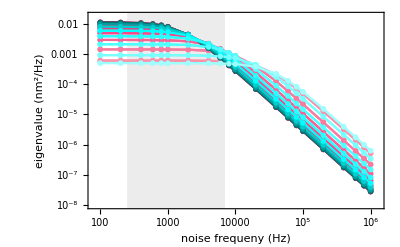

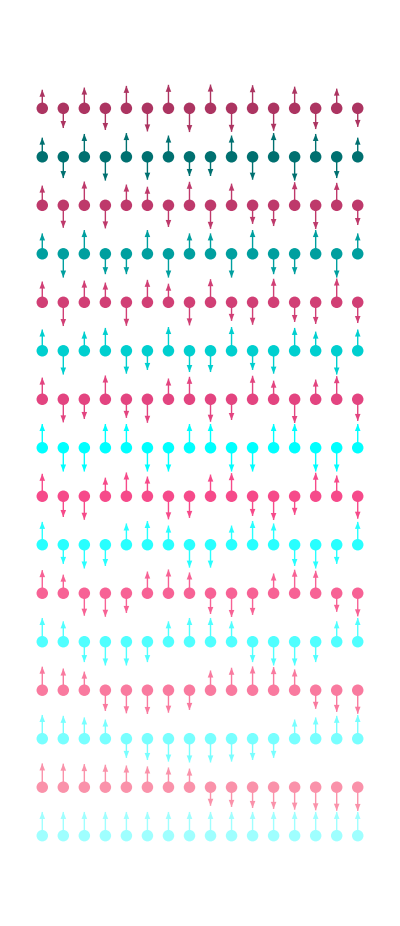

```mathematica
(*Fig.7 plots of eigenvalues vs frequency and symmetric/antysimmetric eigenvectors*)

(*plot settings*)

bar = Blend[{{0, RGBColor[0.25,0,0.25]},{1/2, RGBColor[255/255,0,255/255]},{1, RGBColor[1,0.625,1]}}, #1] &;
bar1=bar /@ (Range[16]/8.)
bar3 = Blend[{{0, RGBColor[0,0.25,0.25]},{1/2, RGBColor[0,255/255,255/255]},{1, RGBColor[0.625,1,1]}}, #1] &;
bar4=bar3 /@ (Range[16]/8.)

bar5 = Blend[{{0, RGBColor[0.60,0.18,0.34]},{1/2,  RGBColor[246/255, 74/255, 138/255]},{1, RGBColor[0.99,0.76,0.75]}}, #1] &;
bar6=bar5 /@ (Range[10]/10.)

plotmarkers=Graphics@{Disk[{0, 0}, Scaled@0.010]};
plotmarkers2=Graphics[Rectangle[Scaled[{0.487,0.487}],Scaled[{0.513,0.513}]]];
plotstylepsd=bar1;
frameticksx={{{1000,Superscript[10,3],{0,0.03}},{10000,Superscript[10,4],{0,0.03}},{100000,Superscript[10,5],{0,0.03}},{2*10^3,,{0,0.02}},{4*10^3,,{0,0.02}},{6*10^3,,{0,0.02}},{8*10^3,,{0,0.02}},{2*10^4,,{0,0.02}},{4*10^4,,{0,0.02}},{6*10^4,,{0,0.02}},{8*10^4,,{0,0.02}}},None};
plotrangeeigenv={{0.8*10^2,1.3*10^6},{10^(-8),1.8*10^(-2)}};
jj=0;
ll=0;

(*separate eigenvectors that are symmetric and antysimmetric*)
For[kk=1,kk<=16,kk++,
If[eigenvandmor[[All,2]][[All,2]][[1,kk]][[8]]/eigenvandmor[[All,2]][[All,2]][[1,kk]][[9]]<0,
jj=jj+1,
ll=ll+1

]
]

(*count eigenvectors*)
jj
ll

(*renormalize and order eigenvectors*)
pp=1;
qq=1;
data1=Table[0,jj];
data2=Table[0,ll];
bar6b=Table[0,16];
For[kk=1,kk<=16,kk++,
If[eigenvandmor[[All,2]][[All,2]][[1,kk]][[8]]/eigenvandmor[[All,2]][[All,2]][[1,kk]][[9]]<0,
data1[[pp]] = Transpose@{eigenvandmor[[All,1]], eigenvandmor[[All,2]][[All,1]][[All,kk]]};
bar6b[[kk]]=bar6[[pp]];
pp=pp+1,
data2[[qq]] = Transpose@{eigenvandmor[[All,1]], eigenvandmor[[All,2]][[All,1]][[All,kk]]};
bar6b[[kk]]=bar4[[qq]];
qq=qq+1

]
]

(*plot settings*)
pady=80;
padx=60;
pad2=30;

(*plot eigenvalues*)
ListLogLogPlot[data1,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotRange->plotrangeeigenv,Joined->True,PlotMarkers->plotmarkers2,PlotStyle->bar6,Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{YTicks, None}, {XTicks, None}},FrameLabel->{"noise frequeny (Hz)", "eigenvalue (\!\(\*SuperscriptBox[\(nm\), \(2\)]\)/Hz)"}
,GridLines -> {{5000}, {}},GridLinesStyle->Directive[RGBColor[0,125/255,128/255],Dashed,Thickness->0.01]];

pl1=Show[%,ListLogLogPlot[data2,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotRange->plotrangeeigenv,Joined->True,PlotMarkers->plotmarkers,PlotStyle-> bar4,Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{YTicks, None}, {XTicks, None}},FrameLabel->{"noise frequeny (Hz)", "eigenvalue (\!\(\*SuperscriptBox[\(nm\), \(2\)]\)/Hz)"}]];
Show[%,ListLogLogPlot[{dl1, dl2}, Joined -> True, 
  PlotRange -> {Automatic, Automatic}, GridLines -> None, 
  PlotStyle -> {White, White}, Filling -> {1 -> {2}}, 
  FillingStyle -> Directive[Opacity[0.15], Gray], ImageSize -> 540]];
Show[%,pl1]

(*plot vibration modes*)

eigenvandrenorm=Table[0,{Length[vecs]},{1}];
max=Table[0,Length[vecs]];
For[kk=1,kk<=Length[vecs],kk++,
max[[kk]]=Max[Abs[eigenvandmor[[All,2]][[All,2]][[1]][[kk]]]];
eigenvandrenorm[[kk]]=eigenvandmor[[All,2]][[All,2]][[1]][[kk]]/max[[kk]];
]
eigenvandrenorm//MatrixForm;
eigenvandrenorm=eigenvandrenorm/11//MatrixForm;
Graphics[{Arrowheads[0.03],Table[{bar6b[[i]],Disk[{j/3, -i/1.3}, 1/11]}, {i,16}, {j,16}],Table[{bar6b[[i]],Arrow[{{j/3,-i/1.3},{j/3,-i/1.3+1/(3.5)*Sign[eigenvandrenorm[[1]][[i]][[j]]]+eigenvandrenorm[[1]][[i]][[j]]}}]},{i,16}, {j,16}]},ImagePadding -> {{pady, pad2}, {padx, pad2}}]
```

0<->-n, low freq, default case

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.02391 | 0.0071343 | 143.519 | 3.11551×10^-10
z | 1.60726 | 0.011315 | 142.047 | 3.28034×10^-10

0.999946

0<->n, low freq, default case

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.02548 | 0.00832769 | 123.141 | 1.93393×10^-11
z | 1.60441 | 0.0131369 | 122.13 | 2.03193×10^-11

0.999912

0<->-n, high freq, default case

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.981717 | 0.0124819 | 78.6513 | 6.2954×10^-9
z | 2.46017 | 0.0366412 | 67.1421 | 1.38771×10^-8

0.999768

0<->n, high freq, default case

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.989153 | 0.00865659 | 114.266 | 3.02886×10^-11
z | 2.42331 | 0.0244199 | 99.235 | 7.05701×10^-11

0.999865

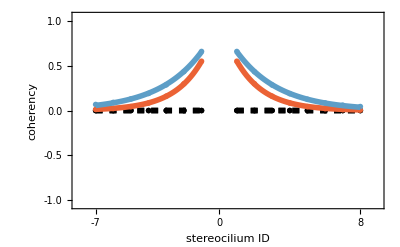

```mathematica
(*Fig8A coherency vs stereocilium ID default case*)

nst=16;

(*define coherency between stereocilia 0 and n at low and high frequency as a function of stereocilium ID with both links*)

coherlowfreq[kk_]:=coherc2[nst,0,kk]/.{w->(2*Pi*10^2),kA1->kA,lA1->lA,kL1->kL,lL1->lL};
coherhighfreq[kk_]:=coherc2[nst,0,kk]/.{w->(2*Pi*10^6),kA1->kA,lA1->lA,kL1->kL,lL1->lL};

(*calculate coherency as a function of stereocilium ID*)
coherlowfreqxy1=Table[{i,coherlowfreq[i]},{i,-7,-1}];
coherhighfreqxy1=Table[{i,coherhighfreq[i]},{i,-7,-1}];
coherlowfreqxy2=Table[{i,coherlowfreq[i]},{i,1,8}];
coherhighfreqxy2=Table[{i,coherhighfreq[i]},{i,1,8}];

(*define coherency between stereocilia 0 and n at low and high frequency as a function of stereocilium ID with no links*)

coherlowfreqall0[kk_]:=coherc2[nst,0,kk]/.{w->(2*Pi*10^2),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL};
coherhighfreqall0[kk_]:=coherc2[nst,0,kk]/.{w->(2*Pi*10^6),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL};

(*calculate coherency as a function of stereocilium ID*)
coherlowfreqxyall01=Table[{i,coherlowfreqall0[i]},{i,-7,-1}];
coherhighfreqxyall01=Table[{i,coherhighfreqall0[i]},{i,-7,-1}];
coherlowfreqxyall02=Table[{i,coherlowfreqall0[i]},{i,1,8}];
coherhighfreqxyall02=Table[{i,coherhighfreqall0[i]},{i,1,8}];

(*plot fig 8A with corresponding fits*)

(*plot settings*)

plotstylecoh2b={{Thickness->0.01,RGBColor[0.922526, 0.385626, 0.209179]},{Thickness->0.01, RGBColor[0.363898, 0.618501, 0.782349]},{Thickness->0.01,RGBColor[0.922526, 0.385626, 0.209179]},{Thickness->0.01,RGBColor[0.363898, 0.618501, 0.782349]}};
plotmarkers=Graphics@{Disk[{0, 0}, Scaled@0.020]};
Remove[XTicks,YTicks]
pady=80;
padx=60;
pad2=30;
XTicks={{-7,-7,{0,TickLength1}},{-6,Null,{0,0.02}},{-5,Null,{0,0.02}},{-4,Null,{0,0.02}},{-3,Null,{0,0.02}},{-2,Null,{0,0.02}},{-1,Null,{0,0.02}},{0,0,{0,TickLength1}},{1,Null,{0,0.02}},{2,Null,{0,0.02}},{3,Null,{0,0.02}},{4,Null,{0,0.02}},{5,Null,{0,0.02}},{6,Null,{0,0.02}},{7,Null,{0,0.02}},{8,8,{0,TickLength1}}};
YTicks={{0.0,"0.0",{0,0.03}},{0.5,0.5,{0,0.03}},{-0.5,-0.5,{0,0.03}},{1.0,"1.0",{0,0.03}},{-1.0,"-1.0",{0,0.03}},{0.1,Null,{0,0.02}},{0.2,Null,{0,0.02}},{0.3,Null,{0,0.02}},{0.4,Null,{0,0.02}},{0.6,Null,{0,0.02}},{0.7,Null,{0,0.02}},{0.8,Null,{0,0.02}},{0.9,Null,{0,0.02}},{-0.1,Null,{0,0.02}},{-0.2,Null,{0,0.02}},{-0.3,Null,{0,0.02}},{-0.4,Null,{0,0.02}},{-0.6,Null,{0,0.02}},{-0.7,Null,{0,0.02}},{-0.8,Null,{0,0.02}},{-0.9,Null,{0,0.02}}};
framelabelslowfreq={{"coherency",None},{"stereocilium ID",None}};
plotrangecoherlowfreq={{-8,9},{-1.05,1.05}};

(*fits of exponential decays*)
Print["0<->-n, low freq, default case"]
fitll = NonlinearModelFit[coherlowfreqxy1, a Exp[x/z], {a, z}, x];
fitll["ParameterTable"]
fitll["RSquared"]

Print["0<->n, low freq, default case"]
fitlr = NonlinearModelFit[coherlowfreqxy2, a Exp[-x/z], {a, z}, x];
fitlr["ParameterTable"]
fitlr["RSquared"]

Print["0<->-n, high freq, default case"]
fithl = NonlinearModelFit[coherhighfreqxy1, a Exp[x/z], {a, z}, x];
fithl["ParameterTable"]
fithl["RSquared"]
 
Print["0<->n, high freq, default case"]
fithr = NonlinearModelFit[coherhighfreqxy2, a Exp[-x/z], {a, z}, x];
fithr["ParameterTable"]
fithr["RSquared"]

(*plots*)
ListPlot[{coherlowfreqxyall01,coherhighfreqxyall01,coherlowfreqxyall02,coherhighfreqxyall02},PlotMarkers->plotmarkers,Joined->True,PlotRange->plotrangecoherlowfreq,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->{{Thickness->0.01,Black,Dashed},{Thickness->0.01,Black,Dashed},{Thickness->0.01,Black,Dashed},{Thickness->0.01,Black,Dashed}},Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameLabel->framelabelslowfreq,FrameTicks -> {{YTicks, None}, {XTicks, None}}];
Show[%,ListPlot[{coherlowfreqxy1,coherhighfreqxy1,coherlowfreqxy2,coherhighfreqxy2},PlotMarkers->plotmarkers,PlotStyle->plotstylecoh2b]];

Show[%,Plot[{fitll[x]}, {x, -7, -1},PlotStyle->{Thickness->0.01, RGBColor[0.922526, 0.385626, 0.209179]}]];
Show[%,Plot[{fitlr[x]}, {x, 1, 8},PlotStyle->{Thickness->0.01, RGBColor[0.922526, 0.385626, 0.209179]}]];
Show[%,Plot[{fithl[x]}, {x, -7, -1},PlotStyle->{Thickness->0.01, RGBColor[0.363898, 0.618501, 0.782349]}]];
Show[%,Plot[{fithr[x]}, {x, 1, 8},PlotStyle->{Thickness->0.01, RGBColor[0.363898, 0.618501, 0.782349]}]]
```

0<->-n, low freq, stiff links only

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.21482 | 0.0341337 | 35.59 | 3.29606×10^-7
z | 3.42746 | 0.128569 | 26.6585 | 1.38866×10^-6

0.998803

0<->n, low freq, stiff links only

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.23246 | 0.0379775 | 32.4523 | 5.69314×10^-8
z | 3.32747 | 0.131146 | 25.3722 | 2.4693×10^-7

0.998189

0<->-n, high freq, stiff links only

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.998869 | 1.49996 | 0.665932 | 0.534941
z | 0.376009 | 0.210752 | 1.78413 | 0.134479

0.94948

0<->n, high freq, stiff links only

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.999231 | 1.37011 | 0.729305 | 0.49329
z | 0.375957 | 0.192388 | 1.95417 | 0.0984884

0.949491

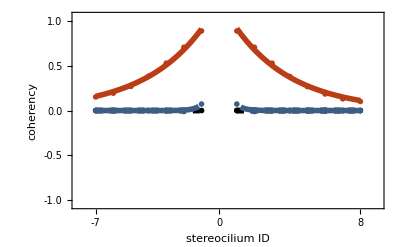

```mathematica
(*Fig8B coherency vs stereocilium ID only stiff links*)

(*define coherency betwwen 0 and n at low and high frequency as a function of stereocilium ID*)
coherlowfreqvisc0[kk_]:=coherc2[nst,0,kk]/.{w->(2*Pi*10^2),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL};
coherhighfreqvisc0[kk_]:=coherc2[nst,0,kk]/.{w->(2*Pi*10^6),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL};

(*calculate coherency as a function of stereocilium ID*)
coherlowfreqxyvisc01=Table[{i,coherlowfreqvisc0[i]},{i,-7,-1}];
coherhighfreqxyvisc01=Table[{i,coherhighfreqvisc0[i]},{i,-7,-1}];
coherlowfreqxyvisc02=Table[{i,coherlowfreqvisc0[i]},{i,1,8}];
coherhighfreqxyvisc02=Table[{i,coherhighfreqvisc0[i]},{i,1,8}];

(*plot fig 8B with corresponding fits*)

(*plot settings*)
Remove[XTicks,YTicks]
pady=80;
padx=60;
pad2=30;
XTicks={{-7,-7,{0,TickLength1}},{-6,Null,{0,0.02}},{-5,Null,{0,0.02}},{-4,Null,{0,0.02}},{-3,Null,{0,0.02}},{-2,Null,{0,0.02}},{-1,Null,{0,0.02}},{0,0,{0,TickLength1}},{1,Null,{0,0.02}},{2,Null,{0,0.02}},{3,Null,{0,0.02}},{4,Null,{0,0.02}},{5,Null,{0,0.02}},{6,Null,{0,0.02}},{7,Null,{0,0.02}},{8,8,{0,TickLength1}}};
YTicks={{0.0,"0.0",{0,0.03}},{0.5,0.5,{0,0.03}},{-0.5,-0.5,{0,0.03}},{1.0,"1.0",{0,0.03}},{-1.0,"-1.0",{0,0.03}},{0.1,Null,{0,0.02}},{0.2,Null,{0,0.02}},{0.3,Null,{0,0.02}},{0.4,Null,{0,0.02}},{0.6,Null,{0,0.02}},{0.7,Null,{0,0.02}},{0.8,Null,{0,0.02}},{0.9,Null,{0,0.02}},{-0.1,Null,{0,0.02}},{-0.2,Null,{0,0.02}},{-0.3,Null,{0,0.02}},{-0.4,Null,{0,0.02}},{-0.6,Null,{0,0.02}},{-0.7,Null,{0,0.02}},{-0.8,Null,{0,0.02}},{-0.9,Null,{0,0.02}}};
framelabelslowfreq={{"coherency",None},{"stereocilium ID",None}};
plotrangecoherlowfreq={{-8,9},{-1.05,1.05}};
plotstylecoh2b={{Thickness->0.01,RGBColor[185/255, 62/255, 23/255]},{Thickness->0.01, RGBColor[60/255, 93/255, 132/255]},{Thickness->0.01,RGBColor[185/255, 62/255, 23/255]},{Thickness->0.01,RGBColor[60/255, 93/255, 132/255]}};

(*fits of exponential decay*)
Print["0<->-n, low freq, stiff links only"]
fitll = NonlinearModelFit[coherlowfreqxyvisc01, a Exp[x/z], {a, z}, x];
fitll["ParameterTable"]
fitll["RSquared"]

Print["0<->n, low freq, stiff links only"]
fitlr = NonlinearModelFit[coherlowfreqxyvisc02, a Exp[-x/z], {a,z}, x];
fitlr["ParameterTable"]
fitlr["RSquared"]

Print["0<->-n, high freq, stiff links only"]
fithl = NonlinearModelFit[coherhighfreqxyvisc01, {a* Exp[x/z],a<1}, {a,z}, x, MaxIterations->100000];
fithl["ParameterTable"]
fithl["RSquared"]

Print["0<->n, high freq, stiff links only"]
fithr = NonlinearModelFit[coherhighfreqxyvisc02, {a* Exp[-x/z],a<1}, {a,z}, x, MaxIterations->100000];
fithr["ParameterTable"]
fithr["RSquared"]

(*plots*)
ListPlot[{coherlowfreqxyall01,coherhighfreqxyall01,coherlowfreqxyall02,coherhighfreqxyall02},PlotMarkers->plotmarkers,Joined->True,PlotRange->plotrangecoherlowfreq,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->{{Thickness->0.01,Gray,Dashed},{Thickness->0.01,Black,Dashed},{Thickness->0.01,Black,Dashed},{Thickness->0.01,Black,Dashed}},Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameLabel->framelabelslowfreq,FrameTicks -> {{YTicks, None}, {XTicks, None}}];
Show[%,ListPlot[{coherlowfreqxyvisc01,coherhighfreqxyvisc01,coherlowfreqxyvisc02,coherhighfreqxyvisc02},PlotMarkers->plotmarkers,PlotStyle->plotstylecoh2b]];

Show[%,Plot[{fitll[x]}, {x, -7, -1},PlotStyle->{Thickness->0.01,RGBColor[185/255, 62/255, 23/255]}]];
Show[%,Plot[{fitlr[x]}, {x, 1, 8},PlotStyle->{Thickness->0.01,RGBColor[185/255, 62/255, 23/255]}]];
Show[%,Plot[{fithl[x]}, {x, -7, -0.3},PlotStyle->{Thickness->0.01, RGBColor[60/255, 93/255, 132/255]}]];
Show[%,Plot[{fithr[x]}, {x, 0.2, 8},PlotStyle->{Thickness->0.01, RGBColor[60/255, 93/255, 132/255]}]]
```

0<->-n, low freq, damped links only

| Estimate | Standard Error | t-Statistic | P-Value
a | 286.114 | 19.6356 | 14.5712 | 0.000027489
z | 0.155344 | 0.00165613 | 93.7996 | 2.61077×10^-9

1.

0<->n, low freq, damped links only

| Estimate | Standard Error | t-Statistic | P-Value
a | 286.114 | 17.9247 | 15.9619 | 3.83924×10^-6
z | 0.155344 | 0.00151183 | 102.752 | 5.72671×10^-11

1.

0<->-n, high freq, damped links only

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.981898 | 0.0124336 | 78.9715 | 6.16887×10^-9
z | 2.45862 | 0.0364616 | 67.4304 | 1.35832×10^-8

0.99977

0<->n, high freq, damped links only

high freq right wing

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.989334 | 0.00860626 | 114.955 | 2.92156×10^-11
z | 2.42183 | 0.0242542 | 99.8522 | 6.79942×10^-11

0.999867

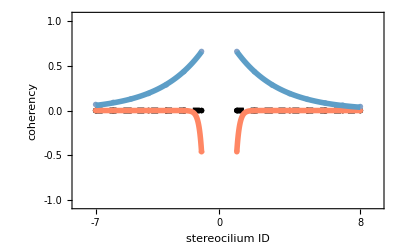

```mathematica
(*Fig8C coherency vs stereocilium ID damped links only*)

(*define coherency between stereocilia 0 and n at low and high frequency as a function of stereocilium ID with damped links only*)
coherlowfreqelas0[kk_]:=coherc2[nst,0,kk]/.{w->(2*Pi*10^2),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL};
coherhighfreqelas0[kk_]:=coherc2[nst,0,kk]/.{w->(2*Pi*10^6),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL};

(*calculate coherency*)
coherlowfreqxyelas01=Table[{i,coherlowfreqelas0[i]},{i,-7,-1}];
coherhighfreqxyelas01=Table[{i,coherhighfreqelas0[i]},{i,-7,-1}];
coherlowfreqxyelas02=Table[{i,coherlowfreqelas0[i]},{i,1,8}];
coherhighfreqxyelas02=Table[{i,coherhighfreqelas0[i]},{i,1,8}];
plotstylecoh2={{Thickness->0.01,RGBColor[0.922526, 0.385626, 0.209179]},{Thickness->0.01, RGBColor[0.363898, 0.618501, 0.782349]},{Thickness->0.01,RGBColor[0.922526, 0.385626, 0.209179]},{Thickness->0.01,RGBColor[0.363898, 0.618501, 0.782349]},{Thickness->0.01, DotDashed,RGBColor[0.922526, 0.385626, 0.209179]},{Thickness->0.01, DotDashed,RGBColor[0.363898, 0.618501, 0.782349]},{Thickness->0.01,DotDashed,RGBColor[0.922526, 0.385626, 0.209179]},{Thickness->0.01, DotDashed,RGBColor[0.363898, 0.618501, 0.782349]}};

(*plot settings*)

Remove[XTicks,YTicks]
pady=80;
padx=60;
pad2=30;
XTicks={{-7,-7,{0,TickLength1}},{-6,Null,{0,0.02}},{-5,Null,{0,0.02}},{-4,Null,{0,0.02}},{-3,Null,{0,0.02}},{-2,Null,{0,0.02}},{-1,Null,{0,0.02}},{0,0,{0,TickLength1}},{1,Null,{0,0.02}},{2,Null,{0,0.02}},{3,Null,{0,0.02}},{4,Null,{0,0.02}},{5,Null,{0,0.02}},{6,Null,{0,0.02}},{7,Null,{0,0.02}},{8,8,{0,TickLength1}}};
YTicks={{0.0,"0.0",{0,0.03}},{0.5,0.5,{0,0.03}},{-0.5,-0.5,{0,0.03}},{1.0,"1.0",{0,0.03}},{-1.0,"-1.0",{0,0.03}},{0.1,Null,{0,0.02}},{0.2,Null,{0,0.02}},{0.3,Null,{0,0.02}},{0.4,Null,{0,0.02}},{0.6,Null,{0,0.02}},{0.7,Null,{0,0.02}},{0.8,Null,{0,0.02}},{0.9,Null,{0,0.02}},{-0.1,Null,{0,0.02}},{-0.2,Null,{0,0.02}},{-0.3,Null,{0,0.02}},{-0.4,Null,{0,0.02}},{-0.6,Null,{0,0.02}},{-0.7,Null,{0,0.02}},{-0.8,Null,{0,0.02}},{-0.9,Null,{0,0.02}}};
framelabelslowfreq={{"coherency",None},{"stereocilium ID",None}};

plotrangecoherlowfreq={{-8,9},{-1.05,1.05}};
plotstylecoh2b={{Thickness->0.01,RGBColor[145/255, 145/255, 145/255]},{Thickness->0.01, RGBColor[145/255, 145/255, 145/255]},{Thickness->0.01,RGBColor[145/255, 145/255, 145/255]},{Thickness->0.01, RGBColor[145/255, 145/255, 145/255]},{Thickness->0.01,RGBColor[255/255, 135/255, 100/255]},{Thickness->0.01, RGBColor[130/255, 162/255, 201/255]},{Thickness->0.01,RGBColor[255/255, 135/255, 100/255]},{Thickness->0.01,RGBColor[130/255, 162/255, 201/255]}};

(*plot 8c with corresponding fits*)

Print["0<->-n, low freq, damped links only"]
fitll = NonlinearModelFit[coherlowfreqxyelas01, {-a*Exp[x/z]}, {a,z}, x, MaxIterations->10000];
fitll["ParameterTable"]
fitll["RSquared"]

Print["0<->n, low freq, damped links only"]
fitlr = NonlinearModelFit[coherlowfreqxyelas02, {-a*Exp[-x/z]}, {a,z}, x, MaxIterations->10000];
fitlr["ParameterTable"]
fitlr["RSquared"]

Print["0<->-n, high freq, damped links only"]
fithl = NonlinearModelFit[coherhighfreqxyelas01, a Exp[x/z], {a, z}, x, MaxIterations->10000];
fithl["ParameterTable"]
fithl["RSquared"]

Print["0<->n, high freq, damped links only"]
Print["high freq right wing"]
fithr = NonlinearModelFit[coherhighfreqxyelas02, a Exp[-x/z], {a, z}, x];
fithr["ParameterTable"]
fithr["RSquared"]

plotstylecoh2b={{Thickness->0.01,RGBColor[255/255, 135/255, 100/255]},{Thickness->0.01, RGBColor[130/255, 162/255, 201/255]},{Thickness->0.01,RGBColor[255/255, 135/255, 100/255]},{Thickness->0.01,RGBColor[130/255, 162/255, 201/255]}};

(*plots*)
ListPlot[{coherlowfreqxyall01,coherhighfreqxyall01,coherlowfreqxyall02,coherhighfreqxyall02},PlotMarkers->plotmarkers,Joined->True,PlotRange->plotrangecoherlowfreq,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->{{Thickness->0.01,Black,Dashed},{Thickness->0.01,Black,Dashed},{Thickness->0.01,Black,Dashed},{Thickness->0.01,Black,Dashed}},Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameLabel->framelabelslowfreq,FrameTicks -> {{YTicks, None}, {XTicks, None}}];
Show[%,ListPlot[{coherlowfreqxyelas01,coherhighfreqxyelas01,coherlowfreqxyelas02,coherhighfreqxyelas02},PlotMarkers->plotmarkers,PlotStyle->plotstylecoh2b]];

Show[%,Plot[{fitll[x]}, {x, -7, 0.1(*-0.2*)},PlotStyle->{Thickness->0.01, RGBColor[255/255, 135/255, 100/255]}]];
Show[%,Plot[{fitlr[x]}, {x, -0.3, 8},PlotStyle->{Thickness->0.01, RGBColor[255/255, 135/255, 100/255]}]];
Show[%,Plot[{fithl[x]}, {x, -7, -1},PlotStyle->{Thickness->0.01, RGBColor[0.363898, 0.618501, 0.782349]}]];
Show[%,Plot[{fithr[x]}, {x, 1, 8},PlotStyle->{Thickness->0.01, RGBColor[0.363898, 0.618501, 0.782349]}]]
```

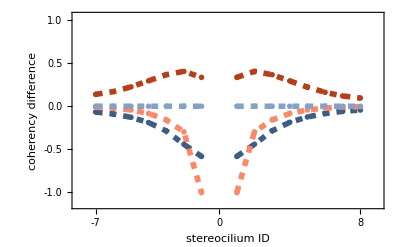

```mathematica
(*Fig8D coherency diffences vs stereocilium ID*)

(*derive coherency differences from previous values*)

coherlowfreq1diffvisc1=Table[{0,0},{Length[coherlowfreqxy1]}];
coherhighfreq1diffvisc1=Table[{0,0},{Length[coherlowfreqxy1]}];
coherlowfreq1diffvisc2=Table[{0,0},{Length[coherlowfreqxy1]+1}];
coherhighfreq1diffvisc2=Table[{0,0},{Length[coherlowfreqxy1]+1}];

For[kk=1,kk<=Length[coherlowfreqxy1],kk++,
coherlowfreq1diffvisc1[[kk]][[1]]=coherlowfreqxy1[[kk]][[1]];
coherlowfreq1diffvisc1[[kk]][[2]]=coherlowfreqxyvisc01[[kk]][[2]]-coherlowfreqxy1[[kk]][[2]];
coherhighfreq1diffvisc1[[kk]][[1]]=coherhighfreqxy1[[kk]][[1]];
coherhighfreq1diffvisc1[[kk]][[2]]=coherhighfreqxyvisc01[[kk]][[2]]-coherhighfreqxy1[[kk]][[2]];
]

For[kk=1,kk<=Length[coherlowfreqxy1]+1,kk++,
coherlowfreq1diffvisc2[[kk]][[1]]=coherlowfreqxy2[[kk]][[1]];
coherlowfreq1diffvisc2[[kk]][[2]]=coherlowfreqxyvisc02[[kk]][[2]]-coherlowfreqxy2[[kk]][[2]];
coherhighfreq1diffvisc2[[kk]][[1]]=coherhighfreqxy2[[kk]][[1]];
coherhighfreq1diffvisc2[[kk]][[2]]=coherhighfreqxyvisc02[[kk]][[2]]-coherhighfreqxy2[[kk]][[2]];

]

coherlowfreq1diffelas1=Table[{0,0},{Length[coherlowfreqxy1]}];
coherhighfreq1diffelas1=Table[{0,0},{Length[coherlowfreqxy1]}];
coherlowfreq1diffelas2=Table[{0,0},{Length[coherlowfreqxy1]+1}];
coherhighfreq1diffelas2=Table[{0,0},{Length[coherlowfreqxy1]+1}];

For[kk=1,kk<=Length[coherlowfreqxy1],kk++,
coherlowfreq1diffelas1[[kk]][[1]]=coherlowfreqxy1[[kk]][[1]];
coherlowfreq1diffelas1[[kk]][[2]]=coherlowfreqxyelas01[[kk]][[2]]-coherlowfreqxy1[[kk]][[2]];
coherhighfreq1diffelas1[[kk]][[1]]=coherhighfreqxy1[[kk]][[1]];
coherhighfreq1diffelas1[[kk]][[2]]=coherhighfreqxyelas01[[kk]][[2]]-coherhighfreqxy1[[kk]][[2]];
]

For[kk=1,kk<=Length[coherlowfreqxy1]+1,kk++,
coherlowfreq1diffelas2[[kk]][[1]]=coherlowfreqxy2[[kk]][[1]];
coherlowfreq1diffelas2[[kk]][[2]]=coherlowfreqxyelas02[[kk]][[2]]-coherlowfreqxy2[[kk]][[2]];
coherhighfreq1diffelas2[[kk]][[1]]=coherhighfreqxy2[[kk]][[1]];
coherhighfreq1diffelas2[[kk]][[2]]=coherhighfreqxyelas02[[kk]][[2]]-coherhighfreqxy2[[kk]][[2]];

]

(*plot settings*)
XTicks={{-7,-7,{0,TickLength1}},{-6,Null,{0,0.02}},{-5,Null,{0,0.02}},{-4,Null,{0,0.02}},{-3,Null,{0,0.02}},{-2,Null,{0,0.02}},{-1,Null,{0,0.02}},{0,0,{0,TickLength1}},{1,Null,{0,0.02}},{2,Null,{0,0.02}},{3,Null,{0,0.02}},{4,Null,{0,0.02}},{5,Null,{0,0.02}},{6,Null,{0,0.02}},{7,Null,{0,0.02}},{8,8,{0,TickLength1}}};
YTicks={{0.0,"0.0",{0,0.03}},{0.5,0.5,{0,0.03}},{-0.5,-0.5,{0,0.03}},{1.0,"1.0",{0,0.03}},{-1.0,"-1.0",{0,0.03}},{0.1,Null,{0,0.02}},{0.2,Null,{0,0.02}},{0.3,Null,{0,0.02}},{0.4,Null,{0,0.02}},{0.6,Null,{0,0.02}},{0.7,Null,{0,0.02}},{0.8,Null,{0,0.02}},{0.9,Null,{0,0.02}},{-0.1,Null,{0,0.02}},{-0.2,Null,{0,0.02}},{-0.3,Null,{0,0.02}},{-0.4,Null,{0,0.02}},{-0.6,Null,{0,0.02}},{-0.7,Null,{0,0.02}},{-0.8,Null,{0,0.02}},{-0.9,Null,{0,0.02}}};

plotstylecohdiff={{Thickness->0.01,RGBColor[185/255, 62/255, 23/255],Dashed},{Thickness->0.01, RGBColor[60/255, 93/255, 132/255],Dashed},{Thickness->0.01,RGBColor[185/255, 62/255, 23/255],Dashed},{Thickness->0.01,RGBColor[60/255, 93/255, 132/255],Dashed},{Thickness->0.01,RGBColor[255/255, 135/255, 100/255],Dashed},{Thickness->0.01, RGBColor[130/255, 162/255, 201/255],Dashed},{Thickness->0.01,RGBColor[255/255, 135/255, 100/255],Dashed},{Thickness->0.01,RGBColor[130/255, 162/255, 201/255],Dashed}};
plotrangecoherlowfreq={{-8,9},{-1.15,1.05}};
framelabelscoherdiff={{"coherency difference",None},{"stereocilium ID",None}};
(*plots*)
ListPlot[{coherlowfreq1diffvisc1,coherhighfreq1diffvisc1,coherlowfreq1diffvisc2,coherhighfreq1diffvisc2,coherlowfreq1diffelas1,coherhighfreq1diffelas1,coherlowfreq1diffelas2,coherhighfreq1diffelas2},Axes->False,Joined->True,PlotMarkers->plotmarkers,PlotRange->plotrangecoherlowfreq,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecohdiff, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameLabel->framelabelscoherdiff,FrameTicks -> {{YTicks, None}, {XTicks, None}}]
```

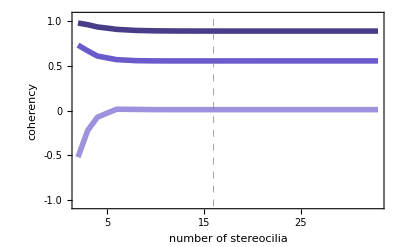

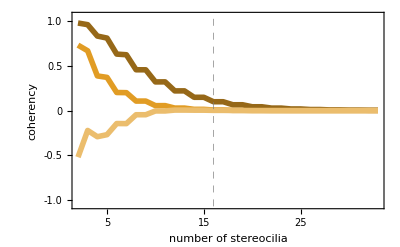

```mathematica
(*Fig 9 plots of coherency vs st number*)

Remove[n]
nmax=33; (*max number of stereocilia*)

(*derive coherency between 0 and 1 and between 0 and 8 as a function of number of stereocilia N*)
coherc01no=coherc2[n,0,1];
coherc08no=coherc2[n,0,IntegerPart[n/2]];

(*calculate values of coherency*)
coher01both=Table[{n,coherc01no/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),kL1->562,lL1->3.646*10^(-3)}},{n,2,nmax}];
coher01stiff=Table[{n,coherc01no/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),kL1->562,lL1->0*3.646*10^(-3)}},{n,2,nmax}];
coher01damp=Table[{n,coherc01no/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),kL1->0*562,lL1->3.646*10^(-3)}},{n,2,nmax}];

coher08both=Table[{n,coherc08no/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),kL1->562,lL1->3.646*10^(-3)}},{n,2,nmax}];
coher08stiff=Table[{n,coherc08no/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),kL1->562,lL1->0*3.646*10^(-3)}},{n,2,nmax}];
coher08damp=Table[{n,coherc08no/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),kL1->0*562,lL1->3.646*10^(-3)}},{n,2,nmax}];

(*plot settings*)
plotstylecoh={Thickness->0.01};

col01= RGBColor[106/255,91/255,205/255];
col08= RGBColor[225/255,156/255,36/255];

plotstylecoh01 = {{Thickness->0.01,
   col01},{Thickness->0.01,
   Darker@col01},{Thickness->0.01,
   Lighter@col01}
   };
   
 
aa=Table[0,{nmax},{4}];
For[k=1,k<=nmax,k++,
aa[[k]]=Table[{l,, {0, TickLength2}}, {l, 1, nmax,1}];
]
Xticks1coh=Table[{k, k, {0, TickLength1}}, {k, 5, 40,5}];

XTickscoh=Union[Xticks1coh,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];

plotrangecoher={{2,nmax},{-1.05,1.05}};

plotstylecoh08 = {{Thickness->0.01,
   col08},{Thickness->0.01,
   Darker@col08},{Thickness->0.01,
   Lighter@col08}
   };

(*plots*)
ListPlot[{coher01both,coher01stiff,coher01damp},Joined->True,PlotRange->plotrangecoher,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh01, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTickscoh,None}},FrameLabel->{"number of stereocilia", "coherency"}
,GridLines -> {{16}, {}}, GridLinesStyle->Directive[Gray,Dashed,Thickness->0.01]]
 
   
(*plots*)
ListPlot[{coher08both,coher08stiff,coher08damp},Joined->True,PlotRange->plotrangecoher,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh08, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTickscoh,None}},FrameLabel->{"number of stereocilia", "coherency"}
,GridLines -> {{16}, {}},GridLines -> {{5000}, {}},GridLinesStyle->Directive[Gray,Dashed,Thickness->0.01]]
```

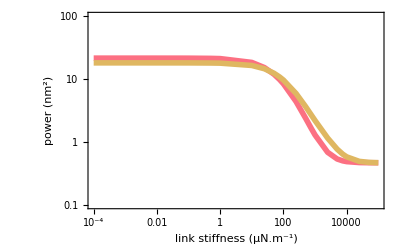

```mathematica
(*Fig 10A-B power of stereocilium 0 and 8 deflection fluctuations vs link stiffness and damping coefficient*)

(*derivation of power spectra*)
psd00=PSDc2[16,0,0];
psd88=PSDc2[16,8,8];

(*range of stiffness values over which to calculate the power*)
kLval={10^-4,5*10^-4,10^-3,5*10^-3,10^-2,5*10^-2,10^-1,5*10^-1,1,10,2.5*10,5*10,7.5*10,10^2,2.5*10^2,5*10^2,7.5*10^2,10^3,2.5*10^3,5*10^3,7.5*10^3,10^4,2.5*10^4,5*10^4,7.5*10^4,10^5};

(*integration of power spectrum of stereocilium 0*)
pow0=Table[0,{Length[kLval]}];
For [jj=1,jj<=Length[kLval],jj++,
psd00temp=Table[{f,psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kLval[[jj]],lL1->lL}}, {f,10,10^7,100}];
pow0[[jj]]={kLval[[jj]],Integrate[Interpolation[psd00temp][x],{x,10,15.91*10^3}]};
];

(*integration of power spectrum of stereocilium 8*)
pow8=Table[0,{Length[kLval]}];
For [jj=1,jj<=Length[kLval],jj++,
psd88temp=Table[{f,psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kLval[[jj]],lL1->lL}}, {f,10,10^7,100}];
pow8[[jj]]={kLval[[jj]],Integrate[Interpolation[psd88temp][x],{x,10,15.91*10^3}]};
];

(*plot settings*)
Yticks1=Table[{10^k, Superscript[10,k], {0, TickLength1}}, {k, -10, 4,1}];
TickLength2=0.02;
aa=Table[0,{20},{4}];
For[k=1,k<=20,k++,
aa[[k]]=Table[{l*10^-(-k+11),, {0, TickLength2}}, {l, 2, 8,2}];
]
YTicks=Union[Yticks1,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];

Xticks1=Table[{10^k, Superscript[10,k], {0, TickLength1}}, {k, -7, 6,2}];
Xticks2=Table[{10^k, Null, {0, TickLength1}}, {k, -8, 8,2}];

XTicks=Union[Xticks1,Xticks2,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];

plotrangepsd={{10^(-4),10^5},{10^(-1),10^(2)}};
plotstylepow={{Thickness->0.01,Lighter[RGBColor[251/255, 41/255, 67/255]]},{Thickness->0.01,RGBColor[223/255, 183/255, 97/255]}};

(*plot*)

ListLogLogPlot[{pow0,pow8},Joined->True,PlotRange->plotrangepsd,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylepow, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{YTicks, None}, {XTicks, None}},FrameLabel->{"link stiffness (μN.\!\(\*SuperscriptBox[\(m\), \(-1\)]\))", "power (\!\(\*SuperscriptBox[\(nm\), \(2\)]\))"},GridLines -> {{562}, {}}, GridLinesStyle->Directive[RGBColor[165/255,97/255,157/255],Dashed,Thickness->0.01]]
```

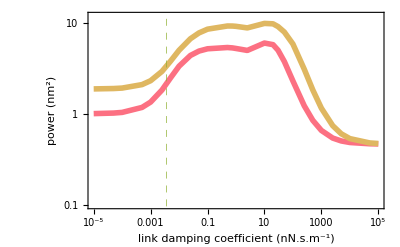

```mathematica
(*Fig 10B power of stereocilium 0 and 1 deflection fluctuations vs link stiffness and damping coefficient*)

(*derivation of power spectra*)
psd00=PSDc2[16,0,0];
psd88=PSDc2[16,8,8];

(*range of stiffness values over which to calculate the power*)
lLval={10^-5,5*10^-5,10^-4,5*10^-4,10^-3,2.5*10^-3,5*10^-3,10^-2,2.5*10^-2,5*10^-2,10^-1,5*10^-1,7.5*10^-1,1,2.5,10^1,2*10^1,3*10^1,5*10^1,10^2,2.5*10^2,5*10^2,10^3,2.5*10^3,5*10^3,10^4,5*10^4,10^5};

(*derivation of power of stereocilium 0 deflection fluctuations*)
pow0lL=Table[0,{Length[lLval]}];
For [jj=1,jj<=Length[lLval],jj++,
psd00temp=Table[{f,psd00/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lLval[[jj]]}}, {f,10,10^7,100}];
pow0lL[[jj]]={lLval[[jj]],Integrate[Interpolation[psd00temp][x],{x,10,15.91*10^3}]};
];

(*derivation of power of stereocilium 8 deflection fluctuations*)
pow8lL=Table[0,{Length[lLval]}];
For [jj=1,jj<=Length[lLval],jj++,
psd88temp=Table[{f,psd88/.{w->(2*Pi*f),kA1->kA,lA1->lA,kL1->kL,lL1->lLval[[jj]]}}, {f,10,10^7,100}];
pow8lL[[jj]]={lLval[[jj]],Integrate[Interpolation[psd88temp][x],{x,10,15.91*10^3}]};
];

(*plot settings*)
Yticks1=Table[{10^k, Superscript[10,k], {0, TickLength1}}, {k, -10, 4,1}];
TickLength2=0.02;
aa=Table[0,{20},{4}];
For[k=1,k<=20,k++,
aa[[k]]=Table[{l*10^-(-k+11),, {0, TickLength2}}, {l, 2, 8,2}];
]
YTicks=Union[Yticks1,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];

Xticks1=Table[{10^k, Superscript[10,k], {0, TickLength1}}, {k, -7, 6,2}];
Xticks2=Table[{10^k, Null, {0, TickLength1}}, {k, -8, 8,2}];

XTicks=Union[Xticks1,Xticks2,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];

plotrangepsd={{10^(-5),10^5},{10^(-1),1.2*10}};
ListLogLogPlot[{pow0lL,pow8lL},Joined->True,PlotRange->plotrangepsd,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylepow, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{YTicks, None}, {XTicks, None}},FrameLabel->{"link damping coefficient (nN.s.\!\(\*SuperscriptBox[\(m\), \(-1\)]\))", "power (\!\(\*SuperscriptBox[\(nm\), \(2\)]\))"},GridLines -> {{3.646*10^(-3)}, {}}, GridLinesStyle->Directive[RGBColor[144/255,176/255,50/255],Dashed,Thickness->0.01]]
```

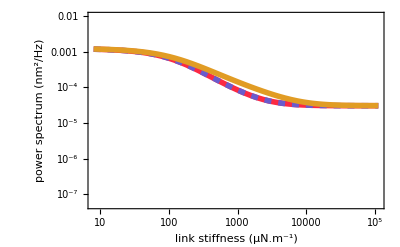

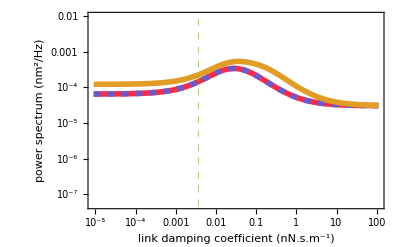

```mathematica
(*Fig C1 power spectra of stereocilia 0, 1, and 8 vs link stiffness and damping coefficient*)


(*plot settings*)
Yticks1=Table[{10^k, Superscript[10,k], {0, TickLength1}}, {k, -10, 1,1}];
TickLength2=0.02;
aa=Table[0,{20},{4}];
For[k=1,k<=20,k++,
aa[[k]]=Table[{l*10^-(-k+11),, {0, TickLength2}}, {l, 2, 8,2}];
]
fff=Union[Yticks1,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];
YTicks=fff;

col00= RGBColor[251/255, 41/255, 67/255];
col01= RGBColor[106/255,91/255,205/255];
col08= RGBColor[225/255,156/255,36/255];

plotstylepsd = {{Thickness->0.01,
   col00},{Thickness->0.01,
   col01,Dashed},{Thickness->0.01,
   col08}
   };
   
Xticks1a=Table[{10^k, Superscript[10,k], {0, TickLength1}}, {k, -10, 10,1}];
XTicksa=Union[Xticks1a,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];

Xticks1b=Table[{10^k, Superscript[10,k], {0, TickLength1}}, {k, -9, 16,2}];(*Table[{i, i, {0, TickLength}}, {i, Xmin, Xmax, 1}];*)
Xticks2b=Table[{10^k, , {0, TickLength1}}, {k, -8, 16,2}];(*Table[{i, i, {0, TickLength}}, {i, Xmin, Xmax, 1}];*)
XTicksb=Union[Xticks1b,Xticks2b,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];

pady=80;
padx=70;
pad2=30;

(*derivation of power spectra of stereocilia 0,1 and 8*)
psd0=PSDc2[16,0,0];
psd1=PSDc2[16,1,1];
psd8=PSDc2[16,8,8];

(*plots*)
   plotrangepsd={{562/70,562*200},{0.5*10^(-7),10^(-2)}};
LogLogPlot[{psd0/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),lL1->3.646*10^(-3)},psd1/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),lL1->3.646*10^(-3)},psd8/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),lL1->3.646*10^(-3)}},
{kL1,562/70,562*200},PlotRange->plotrangepsd,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylepsd, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{YTicks,None}, {XTicksa,None}},FrameLabel->{"link stiffness (μN.\!\(\*SuperscriptBox[\(m\), \(-1\)]\))", "power spectrum (\!\(\*SuperscriptBox[\(nm\), \(2\)]\)/Hz)"}
,GridLines -> {{562}, {}}, GridLinesStyle->Directive[RGBColor[165/255,97/255,157/255],Dashed,Thickness->0.01]]

 plotrangepsd={{3.646*10^(-3)/400,3.646*10^(-3)*30000},{0.5*10^(-7),10^(-2)}};
LogLogPlot[{psd0/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),kL1->562},psd1/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),kL1->562},psd8/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),kL1->562}},
{lL1,3.646*10^(-3)/400,3.646*10^(-3)*30000},PlotRange->plotrangepsd,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylepsd, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {{YTicks,None}, {XTicksb,None}},FrameLabel->{"link damping coefficient (nN.s.\!\(\*SuperscriptBox[\(m\), \(-1\)]\))", "power spectrum (\!\(\*SuperscriptBox[\(nm\), \(2\)]\)/Hz)"}
,GridLines -> {{3.646*10^(-3)}, {}}, GridLinesStyle->Directive[RGBColor[144/255,176/255,50/255],Dashed,Thickness->0.01]]
```

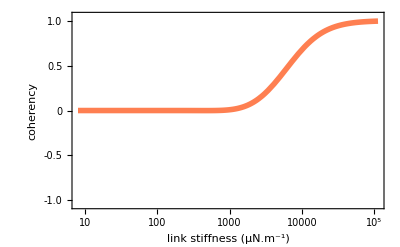

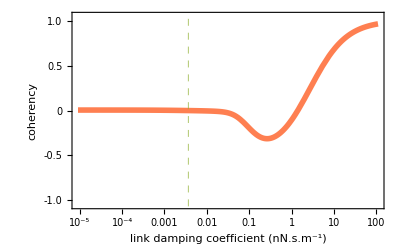

```mathematica
(*Fig C2 of power spectrum betwween -7 and 8 vs link stiffness and damping coefficient*)

(*calculate coherency*)
coherm7p8=coherc2[16,-7,8];

(*plot settings*)
plotstylecoh={Thickness->0.01};

col01= RGBColor[254/255,127/255,81/255];

plotstylecoh01 = {{Thickness->0.01,
   col01}
   }; 

pady=80;
padx=70;
pad2=30;

aa=Table[0,{20},{4}];
For[k=1,k<=20,k++,
aa[[k]]=Table[{l*10^-(-k+11),, {0, TickLength2}}, {l, 2, 8,2}];
]      
Remove[XTicksa,Xticks1a]
Xticks1a=Table[{10^k, Superscript[10,k], {0, TickLength1}}, {k, -10, 10,1}];
XTicksa=Union[Xticks1a,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];
plotrangecoher1={{562/70,562*200},{-1.05,1.05}};

(*plots*)
LogLinearPlot[coherm7p8/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),lL1->3.646*10^(-3)},
{kL1,562/70,562*200},PlotRange->plotrangecoher1,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh01, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicksa,None}},FrameLabel->{"link stiffness (μN.\!\(\*SuperscriptBox[\(m\), \(-1\)]\))", "coherency"}
,GridLines -> {{562}, {}}, GridLinesStyle->Directive[RGBColor[165/255,97/255,157/255],Dashed,Thickness->0.01]]

Remove[XTicksb,Xticks1b,Xticks2b]
Xticks1b=Table[{10^k, Superscript[10,k], {0, TickLength1}}, {k, -9, 16,2}];(*Table[{i, i, {0, TickLength}}, {i, Xmin, Xmax, 1}];*)
Xticks2b=Table[{10^k, , {0, TickLength1}}, {k, -8, 16,2}];(*Table[{i, i, {0, TickLength}}, {i, Xmin, Xmax, 1}];*)
XTicksb=Union[Xticks1b,Xticks2b,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];
plotrangecoher2={{3.646*10^(-3)/400,3.646*10^(-3)*30000},{-1.05,1.05}};

LogLinearPlot[coherm7p8/.{w->5000*2*Pi,kA1->146.3,kL1->562,lA1->6.563*10^(-4)},
{lL1,3.646*10^(-3)/400,3.646*10^(-3)*30000},PlotRange->plotrangecoher2,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh01, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTicksb,None}},FrameLabel->{"link damping coefficient (nN.s.\!\(\*SuperscriptBox[\(m\), \(-1\)]\))", "coherency"}
,GridLines -> {{3.646*10^(-3)}, {}}, GridLinesStyle->Directive[RGBColor[144/255,176/255,50/255],Dashed,Thickness->0.01]]
```

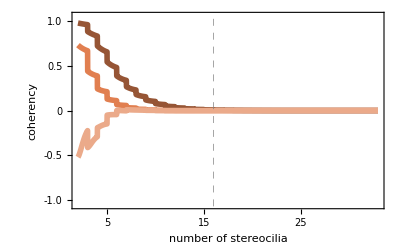

```mathematica
(*Fig C3 coherency between -Nl and Nr as a function of the number of stereocilia*)
Remove[n]
cohercnlnr=coherc2[n, IntegerPart[-(n-1)/2], IntegerPart[(n)/2]];

nmax=33; (*maximum number of stereocilia*)
(*plot settings*)
plotstylecoh={Thickness->0.01};

colnlnr= RGBColor[225/255,127/255,80/255];

(*plot settings*)
aa=Table[0,{nmax},{4}];
For[k=1,k<=nmax,k++,
aa[[k]]=Table[{l,, {0, TickLength2}}, {l, 1, nmax,1}];
]
Xticks1coh=Table[{k, k, {0, TickLength1}}, {k, 5, 40,5}];(*Table[{i, i, {0, TickLength}}, {i, Xmin, Xmax, 1}];*)

XTickscoh=Union[Xticks1coh,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];

plotrangecoher={{2,nmax},{-1.05,1.05}};

plotstylecoh08 = {{Thickness->0.01,
   colnlnr},{Thickness->0.01,
   Darker@colnlnr},{Thickness->0.01,
   Lighter@colnlnr}
   };
   
(*plot*)
Plot[{cohercnlnr/.{w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),kL1->562,lL1->3.646*10^(-3)},cohercnlnr/.{N->n,w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),kL1->562,lL1->0*3.646*10^(-3)},cohercnlnr/.{N->n,w->5000*2*Pi,kA1->146.3,lA1->6.563*10^(-4),kL1->0*562,lL1->3.646*10^(-3)}},
{n,2,nmax},PlotRange->plotrangecoher,Axes->False,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotStyle->plotstylecoh08, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameTicks -> {frameticksycoherneg, {XTickscoh,None}},FrameLabel->{"number of stereocilia", "coherency"}
,GridLines -> {{16}, {}},GridLines -> {{5000}, {}},GridLinesStyle->Directive[Gray,Dashed,Thickness->0.01]]
```

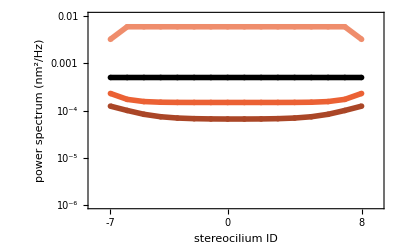

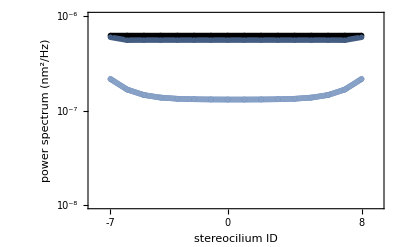

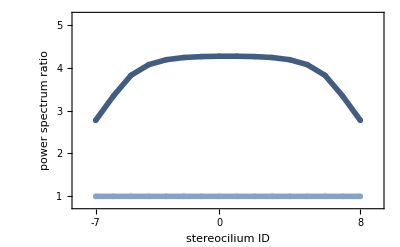

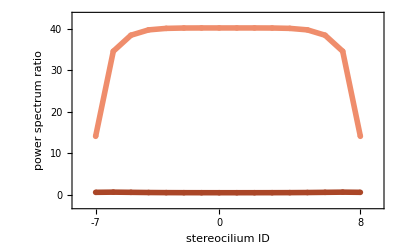

```mathematica
(*Fig C4 coherency at low and high frequency as a function of stereocilium pair*)
nst=16;
(*derivation of power spectra at low and high frequency vs stereocilium ID with both links*)
psdlowfreq[kk_]:=PSDc2[nst,kk,kk]/.{w->(2*Pi*10^2),kA1->kA,lA1->lA,kL1->kL,lL1->lL};
psdhighfreq[kk_]:=PSDc2[nst,kk,kk]/.{w->(2*Pi*10^6),kA1->kA,lA1->lA,kL1->kL,lL1->lL};
psdlowfreqall0[kk_]:=PSDc2[nst,kk,kk]/.{w->(2*Pi*10^2),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL};
psdhighfreqall0[kk_]:=PSDc2[nst,kk,kk]/.{w->(2*Pi*10^6),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL};
psdlowfreqxyall0=Table[{i,psdlowfreqall0[i]},{i,-7,8}];
psdhighfreqxyall0=Table[{i,psdhighfreqall0[i]},{i,-7,8}];
psdlowfreqvisc0[kk_]:=PSDc2[nst,kk,kk]/.{w->(2*Pi*10^2),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL};
psdhighfreqvisc0[kk_]:=PSDc2[nst,kk,kk]/.{w->(2*Pi*10^6),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL};
psdlowfreqxyvisc0=Table[{i,psdlowfreqvisc0[i]},{i,-7,8}];
psdhighfreqxyvisc0=Table[{i,psdhighfreqvisc0[i]},{i,-7,8}];

psdlowfreqxy=Table[{i,psdlowfreq[i]},{i,-7,8}];
psdhighfreqxy=Table[{i,psdhighfreq[i]},{i,-7,8}];
plotstylecoh1b={{Thickness->0.01,RGBColor[0.368417, 0.506779, 0.709798]}};

psdlowfreqxyvisc0ratio=Table[0,{Length[psdlowfreqxy]},{2}];
For[kk=1,kk<=Length[psdlowfreqxy],kk++,
(*derivation of the power spectra ratio*)
psdlowfreqxyvisc0ratio[[kk]][[1]]=psdlowfreqxyvisc0[[kk]][[1]];
psdlowfreqxyvisc0ratio[[kk]][[2]]=psdlowfreqxyvisc0[[kk]][[2]]/psdlowfreqxy[[kk]][[2]];
]

psdhighfreqxyvisc0ratio=Table[0,{Length[psdhighfreqxy]},{2}];
For[kk=1,kk<=Length[psdhighfreqxy],kk++,
(*derivation of the power spectra ratio*)
psdhighfreqxyvisc0ratio[[kk]][[1]]=psdhighfreqxyvisc0[[kk]][[1]];
psdhighfreqxyvisc0ratio[[kk]][[2]]=psdhighfreqxyvisc0[[kk]][[2]]/psdhighfreqxy[[kk]][[2]];
]
(*psdlowfreqelas0=Table[0,{15}];
psdhighfreqelas0=Table[0,{15}];*)
psdlowfreqelas0[kk_]:=PSDc2[nst,kk,kk]/.{w->(2*Pi*10^2),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL};
psdhighfreqelas0[kk_]:=PSDc2[nst,kk,kk]/.{w->(2*Pi*10^6),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL};
psdlowfreqxyelas0=Table[{i,psdlowfreqelas0[i]},{i,-7,8}];
psdhighfreqxyelas0=Table[{i,psdhighfreqelas0[i]},{i,-7,8}];

(*plot settings*)
TickLength2=0.02;
aa=Table[0,{20},{4}];
For[k=1,k<=20,k++,
aa[[k]]=Table[{l*10^-(-k+11),l "*"Superscript[10,-7], {0, TickLength2}}, {l, 2, 9,2}];
]

fff=Union[Yticks1,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];
YTicks=fff;
plotrangepsdlowfreq={{-8,9},{1*10^(-7),1*10^(-6)}};

Yticks1=Table[{10^k, Superscript[10,k], {0, TickLength1}}, {k, -8, 1,1}];
TickLength2=0.02;
aa=Table[0,{20},{4}];
For[k=1,k<=20,k++,
aa[[k]]=Table[{l*10^-(-k+18),, {0, TickLength2}}, {l, 2, 8,2}];
]
fff=Union[Yticks1,aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]],aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]],aa[[14]],aa[[15]],aa[[16]],aa[[17]],aa[[18]],aa[[19]],aa[[20]]];
YTicks={{1/50000000000000000,Null,{0,0.02}},{1/25000000000000000,Null,{0,0.02}},{3/50000000000000000,Null,{0,0.02}},{1/12500000000000000,Null,{0,0.02}},{1/5000000000000000,Null,{0,0.02}},{1/2500000000000000,Null,{0,0.02}},{3/5000000000000000,Null,{0,0.02}},{1/1250000000000000,Null,{0,0.02}},{1/500000000000000,Null,{0,0.02}},{1/250000000000000,Null,{0,0.02}},{3/500000000000000,Null,{0,0.02}},{1/125000000000000,Null,{0,0.02}},{1/50000000000000,Null,{0,0.02}},{1/25000000000000,Null,{0,0.02}},{3/50000000000000,Null,{0,0.02}},{1/12500000000000,Null,{0,0.02}},{1/5000000000000,Null,{0,0.02}},{1/2500000000000,Null,{0,0.02}},{3/5000000000000,Null,{0,0.02}},{1/1250000000000,Null,{0,0.02}},{1/500000000000,Null,{0,0.02}},{1/250000000000,Null,{0,0.02}},{3/500000000000,Null,{0,0.02}},{1/125000000000,Null,{0,0.02}},{1/50000000000,Null,{0,0.02}},{1/25000000000,Null,{0,0.02}},{3/50000000000,Null,{0,0.02}},{1/12500000000,Null,{0,0.02}},{1/5000000000,Null,{0,0.02}},{1/2500000000,Null,{0,0.02}},{3/5000000000,Null,{0,0.02}},{1/1250000000,Null,{0,0.02}},{1/500000000,Null,{0,0.02}},{1/250000000,Null,{0,0.02}},{3/500000000,Null,{0,0.02}},{1/125000000,Null,{0,0.02}},{1/100000000,Superscript[10,-8],{0,0.03}},{1/50000000,Null,{0,0.02}},{1/25000000,Null,{0,0.02}},{3/50000000,Null,{0,0.02}},{1/12500000,Null,{0,0.02}},{1/10000000,Superscript[10,-7],{0,0.03}},{1/5000000,Null,{0,0.02}},{1/2500000,Null,{0,0.02}},{3/5000000,Null,{0,0.02}},{1/1250000,Null,{0,0.02}},{1/1000000,Superscript[10,-6],{0,0.03}},{1/500000,Null,{0,0.02}},{1/250000,Null,{0,0.02}},{3/500000,Null,{0,0.02}},{1/125000,Null,{0,0.02}},{1/100000,Superscript[10,-5],{0,0.03}},{1/50000,Null,{0,0.02}},{1/25000,Null,{0,0.02}},{3/50000,Null,{0,0.02}},{1/12500,Null,{0,0.02}},{1/10000,Superscript[10,-4],{0,0.03}},{1/5000,Null,{0,0.02}},{1/2500,Null,{0,0.02}},{3/5000,Null,{0,0.02}},{1/1250,Null,{0,0.02}},{1/1000,Superscript[10,-3],{0,0.03}},{1/500,Null,{0,0.02}},{1/250,Null,{0,0.02}},{3/500,Null,{0,0.02}},{1/125,Null,{0,0.02}},{1/100,Superscript[10,-2],{0,0.03}},{1/50,Null,{0,0.02}},{1/25,Null,{0,0.02}},{3/50,Null,{0,0.02}},{2/25,Null,{0,0.02}},{1/10,Superscript[10,-1],{0,0.03}},{1/5,Null,{0,0.02}},{2/5,Null,{0,0.02}},{3/5,Null,{0,0.02}},{4/5,Null,{0,0.02}},{1,Superscript[10,0],{0,0.03}},{2,Null,{0,0.02}},{4,Null,{0,0.02}},{6,Null,{0,0.02}},{8,Null,{0,0.02}},{10,Superscript[10,1],{0,0.03}},{20,Null,{0,0.02}},{40,Null,{0,0.02}},{60,Null,{0,0.02}},{80,Null,{0,0.02}},{200,Null,{0,0.02}},{400,Null,{0,0.02}},{600,Null,{0,0.02}},{800,Null,{0,0.02}}};
plotrangepsdlowfreq={{-8,9},{10^(-6),10^(-2)}};
plotstylepsd2={{Thickness->0.01,RGBColor[235/255, 97/255,52/255]},{Thickness->0.01, Black},{Thickness->0.01,RGBColor[239/255, 141/255,108/255]},{Thickness->0.01,RGBColor[170/255, 70/255,39/255]}};
framelabelslowfreq={{"power spectrum (\!\(\*SuperscriptBox[\(nm\), \(2\)]\)/Hz)",None},{"stereocilium ID",None}};
plotmarkers=Graphics@{Disk[{0, 0}, Scaled@0.020]};
XTicks={{-7,-7,{0,TickLength1}},{-6,Null,{0,0.02}},{-5,Null,{0,0.02}},{-4,Null,{0,0.02}},{-3,Null,{0,0.02}},{-2,Null,{0,0.02}},{-1,Null,{0,0.02}},{0,0,{0,TickLength1}},{1,Null,{0,0.02}},{2,Null,{0,0.02}},{3,Null,{0,0.02}},{4,Null,{0,0.02}},{5,Null,{0,0.02}},{6,Null,{0,0.02}},{7,Null,{0,0.02}},{8,8,{0,TickLength1}}};

(*plots*)
ListLogPlot[{psdlowfreqxy,psdlowfreqxyall0,psdlowfreqxyelas0,psdlowfreqxyvisc0},Axes->False,PlotRange->plotrangepsdlowfreq,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},Joined->True,PlotMarkers->plotmarkers,PlotStyle->plotstylepsd2, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameLabel->framelabelslowfreq,FrameTicks -> {{YTicks, None}, {XTicks, None}}](*,FrameLabel->framelabels*)
plotrangepsdlowfreq={{-8,9},{1*10^(-8),1*10^(-6)}};
plotstylepsd2={{Thickness->0.01,RGBColor[94/255, 129/255,181/255]},{Thickness->0.01, Black},{Thickness->0.01, RGBColor[136/255, 161/255,198/255]},{Thickness->0.01,RGBColor[67/255, 92/255,129/255]}};
ListLogPlot[{psdhighfreqxy,psdhighfreqxyall0,psdhighfreqxyelas0,psdhighfreqxyvisc0},Axes->False,PlotRange->plotrangepsdlowfreq,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},Joined->True,PlotMarkers->plotmarkers,PlotStyle->plotstylepsd2, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameLabel->framelabelslowfreq,FrameTicks -> {{YTicks, None}, {XTicks, None}}](*,FrameLabel->framelabels*)

(*Fig S3B & D power spectra ratio at low and high frequencies*)

(*derivation of power spectra ratio from previous results*)
psdlowfreqxyelas0ratio=Table[0,{Length[psdlowfreqxy]},{2}];
For[kk=1,kk<=Length[psdlowfreqxy],kk++,

psdlowfreqxyelas0ratio[[kk]][[1]]=psdlowfreqxyelas0[[kk]][[1]];
psdlowfreqxyelas0ratio[[kk]][[2]]=psdlowfreqxyelas0[[kk]][[2]]/psdlowfreqxy[[kk]][[2]];
]

psdhighfreqxyelas0ratio=Table[0,{Length[psdhighfreqxy]},{2}];
plotrangehighfreqratio={{-8,9},{0.8,5.2}};
framelabelspsdratios={{"power spectrum ratio",None},{"stereocilium ID",None}};

For[kk=1,kk<=Length[psdhighfreqxy],kk++,

psdhighfreqxyelas0ratio[[kk]][[1]]=psdhighfreqxyelas0[[kk]][[1]];
psdhighfreqxyelas0ratio[[kk]][[2]]=psdhighfreqxyelas0[[kk]][[2]]/psdhighfreqxy[[kk]][[2]];
]

(*plot settings*)
YTicks={{1,1,{0,0.03}},{2,2,{0,0.03}},{3,3,{0,0.03}},{4,4,{0,0.03}},{5,5,{0,0.03}},{1.2,Null,{0,0.02}},{1.4,Null,{0,0.02}},{1.6,Null,{0,0.02}},{1.8,Null,{0,0.02}},{2.2,Null,{0,0.02}},{2.4,Null,{0,0.02}},{2.6,Null,{0,0.02}},{2.8,Null,{0,0.02}},{3.2,Null,{0,0.02}},{3.4,Null,{0,0.02}},{3.6,Null,{0,0.02}},{3.8,Null,{0,0.02}},{4.2,Null,{0,0.02}},{4.4,Null,{0,0.02}},{4.6,Null,{0,0.02}},{4.8,Null,{0,0.02}}};
XTicks={{-7,-7,{0,TickLength1}},{-6,Null,{0,0.02}},{-5,Null,{0,0.02}},{-4,Null,{0,0.02}},{-3,Null,{0,0.02}},{-2,Null,{0,0.02}},{-1,Null,{0,0.02}},{0,0,{0,TickLength1}},{1,Null,{0,0.02}},{2,Null,{0,0.02}},{3,Null,{0,0.02}},{4,Null,{0,0.02}},{5,Null,{0,0.02}},{6,Null,{0,0.02}},{7,Null,{0,0.02}},{8,8,{0,TickLength1}}};
plotstylepsd2={{Thickness->0.01,RGBColor[136/255, 161/255,198/255]},{Thickness->0.01,RGBColor[67/255, 92/255,129/255]}};
ListPlot[{psdhighfreqxyelas0ratio,psdhighfreqxyvisc0ratio},Axes->False,PlotRange->plotrangehighfreqratio,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},Joined->True,PlotMarkers->plotmarkers,PlotStyle->plotstylepsd2, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameLabel->framelabelspsdratios,FrameTicks -> {{YTicks, None}, {XTicks, None}}](*,FrameLabel->framelabels*)

plotrangehighfreqratio={{-8,9},{-2.5,43}};
YTicks={{0,0,{0,0.03}},{5,5,{0,0.03}},{10,10,{0,0.03}},{15,15,{0,0.03}},{20,20,{0,0.03}},{25,25,{0,0.03}},{30,30,{0,0.03}},{35,35,{0,0.03}},{40,40,{0,0.03}},{2.5,Null,{0,0.02}},{7.5,Null,{0,0.02}},{12.5,Null,{0,0.02}},{17.5,Null,{0,0.02}},{22.5,Null,{0,0.02}},{27.5,Null,{0,0.02}},{32.5,Null,{0,0.02}},{37.5,Null,{0,0.02}},{42.5,Null,{0,0.02}}};

XTicks={{-7,-7,{0,TickLength1}},{-6,Null,{0,0.02}},{-5,Null,{0,0.02}},{-4,Null,{0,0.02}},{-3,Null,{0,0.02}},{-2,Null,{0,0.02}},{-1,Null,{0,0.02}},{0,0,{0,TickLength1}},{1,Null,{0,0.02}},{2,Null,{0,0.02}},{3,Null,{0,0.02}},{4,Null,{0,0.02}},{5,Null,{0,0.02}},{6,Null,{0,0.02}},{7,Null,{0,0.02}},{8,8,{0,TickLength1}}};
plotstylepsd2={{Thickness->0.01, RGBColor[170/255, 70/255,39/255]},{Thickness->0.01,RGBColor[239/255, 141/255,108/255]}};

(*plots*)
ListPlot[{psdlowfreqxyvisc0ratio,psdlowfreqxyelas0ratio},Axes->False,PlotRange->plotrangehighfreqratio,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},Joined->True,PlotMarkers->plotmarkers,PlotStyle->plotstylepsd2, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameLabel->framelabelspsdratios,FrameTicks -> {{YTicks, None}, {XTicks, None}}](*,FrameLabel->framelabels*)
```

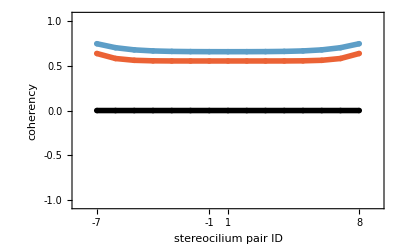

```mathematica
(*Figure C5A coherency between stereocilium pairs with stiff links*)

(*derivation of coherency vs stereocilium pairs*)

coherlowfreqall0pairs[kk_]:=coherc2[16,kk,kk+1]/.{w->(2*Pi*10^2),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL};
coherhighfreqall0pairs[kk_]:=coherc2[16,kk,kk+1]/.{w->(2*Pi*10^6),kA1->kA,lA1->lA,kL1->0*kL,lL1->0*lL};

coherlowfreqxyall0pairs=Table[{i,coherlowfreqall0pairs[i]},{i,-7,7}];
coherhighfreqxyall0pairs=Table[{i,coherhighfreqall0pairs[i]},{i,-7,7}];

coherlowfreqpairs[kk_]:=coherc2[16,kk,kk+1]/.{w->(2*Pi*10^2),kA1->kA,lA1->lA,kL1->kL,lL1->lL};
coherhighfreqpairs[kk_]:=coherc2[16,kk,kk+1]/.{w->(2*Pi*10^6),kA1->kA,lA1->lA,kL1->kL,lL1->lL};

coherlowfreqxypairs=Table[{i,coherlowfreqpairs[i]},{i,-7,7}];
coherhighfreqxypairs=Table[{i,coherhighfreqpairs[i]},{i,-7,7}];

(*plot settings*)
plotstylecoh={{Thickness->0.01, RGBColor[0.922526, 0.385626, 0.209179]},{Thickness->0.01, RGBColor[0.363898, 0.618501, 0.782349]},{Thickness->0.01,  Black}};

Remove[XTicks,YTicks]
plotmarkers=Graphics@{Disk[{0, 0}, Scaled@0.020]};
pady=80;
padx=60;
pad2=30;

XTicks={{-7,-7,{0,TickLength1}},{-6,Null,{0,0.02}},{-5,Null,{0,0.02}},{-4,Null,{0,0.02}},{-3,Null,{0,0.02}},{-2,Null,{0,0.02}},{-1,-1,{0,TickLength1}},{0,1,{0,0.02}},{1,Null,{0,TickLength2}},{2,Null,{0,0.02}},{3,Null,{0,0.02}},{4,Null,{0,0.02}},{5,Null,{0,0.02}},{6,Null,{0,0.02}},{7,8,{0,0.03}}};

YTicks={{0.0,"0.0",{0,0.03}},{0.5,0.5,{0,0.03}},{-0.5,-0.5,{0,0.03}},{1.0,"1.0",{0,0.03}},{-1.0,"-1.0",{0,0.03}},{0.1,Null,{0,0.02}},{0.2,Null,{0,0.02}},{0.3,Null,{0,0.02}},{0.4,Null,{0,0.02}},{0.6,Null,{0,0.02}},{0.7,Null,{0,0.02}},{0.8,Null,{0,0.02}},{0.9,Null,{0,0.02}},{-0.1,Null,{0,0.02}},{-0.2,Null,{0,0.02}},{-0.3,Null,{0,0.02}},{-0.4,Null,{0,0.02}},{-0.6,Null,{0,0.02}},{-0.7,Null,{0,0.02}},{-0.8,Null,{0,0.02}},{-0.9,Null,{0,0.02}}};
framelabelslowfreq={{"coherency",None},{"stereocilium pair ID",None}};

plotrangecoherlowfreq={{-8,8},{-1.05,1.05}};

(*plot*)
ListPlot[{coherlowfreqxypairs,coherhighfreqxypairs,coherlowfreqxyall0pairs},PlotRange->plotrangecoherlowfreq,Axes->{False,False},ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotMarkers->plotmarkers,Joined->True,PlotStyle->plotstylecoh, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],
FrameLabel->framelabelslowfreq,FrameTicks -> {{YTicks, None}, {XTicks, None}}]
```

```mathematica
(*Figure C5B coherency between stereocilium pairs with both links*)

(*derivation of coherency vs stereocilium pairs*)

coherlowfreqpairs[kk]:=coherc[16,kk,kk+1]/.{w->(2*Pi*10^2),kA1->kA,lA1->lA,kL1->kL,lL1->lL};
coherhighfreqpairs[kk]:=coherc[16,kk,kk+1]/.{w->(2*Pi*10^6),kA1->kA,lA1->lA,kL1->kL,lL1->lL};

coherlowfreqxypairs=Table[{i,coherlowfreqpairs[i]},{i,-7,7}];
coherhighfreqxypairs=Table[{i,coherhighfreqpairs[i]},{i,-7,7}];

(*plot settings*)
plotstylecoh={{Thickness->0.01, RGBColor[0.922526, 0.385626, 0.209179]},{Thickness->0.01, RGBColor[0.363898, 0.618501, 0.782349]},{Thickness->0.01,  Black}};

Remove[XTicks,YTicks]
plotmarkers=Graphics@{Disk[{0, 0}, Scaled@0.020]};
pady=80;
padx=60;
pad2=30;

XTicks={{-7,-7,{0,TickLength1}},{-6,Null,{0,0.02}},{-5,Null,{0,0.02}},{-4,Null,{0,0.02}},{-3,Null,{0,0.02}},{-2,Null,{0,0.02}},{-1,-1,{0,TickLength1}},{0,1,{0,0.02}},{1,Null,{0,TickLength2}},{2,Null,{0,0.02}},{3,Null,{0,0.02}},{4,Null,{0,0.02}},{5,Null,{0,0.02}},{6,Null,{0,0.02}},{7,8,{0,0.03}}};
YTicks={{0.0,"0.0",{0,0.03}},{0.5,0.5,{0,0.03}},{-0.5,-0.5,{0,0.03}},{1.0,"1.0",{0,0.03}},{-1.0,"-1.0",{0,0.03}},{0.1,Null,{0,0.02}},{0.2,Null,{0,0.02}},{0.3,Null,{0,0.02}},{0.4,Null,{0,0.02}},{0.6,Null,{0,0.02}},{0.7,Null,{0,0.02}},{0.8,Null,{0,0.02}},{0.9,Null,{0,0.02}},{-0.1,Null,{0,0.02}},{-0.2,Null,{0,0.02}},{-0.3,Null,{0,0.02}},{-0.4,Null,{0,0.02}},{-0.6,Null,{0,0.02}},{-0.7,Null,{0,0.02}},{-0.8,Null,{0,0.02}},{-0.9,Null,{0,0.02}}};
framelabelslowfreq={{"coherency",None},{"stereocilium pair ID",None}};

plotrangecoherlowfreq={{-8,8},{-1.05,1.05}};

(*plot*)
ListPlot[{coherlowfreqxypairs,coherhighfreqxypairs,coherlowfreqxyall0pairs},PlotRange->plotrangecoherlowfreq,Axes->{False,False},ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},PlotMarkers->plotmarkers,Joined->True,PlotStyle->plotstylecoh, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],
FrameLabel->framelabelslowfreq,FrameTicks -> {{YTicks, None}, {XTicks, None}}]
```

-Graphics-

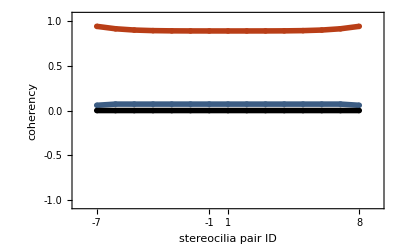

```mathematica
(*Figure C5C coherency between stereocilium pairs with damped links only*)

(*derivation of coherency vs stereocilium pairs*)
coherlowfreqvisc0pairs[kk_]:=coherc2[16,kk,kk+1]/.{w->(2*Pi*10^2),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL};
coherhighfreqvisc0pairs[kk_]:=coherc2[16,kk,kk+1]/.{w->(2*Pi*10^6),kA1->kA,lA1->lA,kL1->kL,lL1->0*lL};

coherlowfreqxyvisc0pairs=Table[{i,coherlowfreqvisc0pairs[i]},{i,-7,7}];
coherhighfreqxyvisc0pairs=Table[{i,coherhighfreqvisc0pairs[i]},{i,-7,7}];

(*plot settings*)
plotstylecoh2={{Thickness->0.01,RGBColor[185/255, 62/255, 23/255]},{Thickness->0.01, RGBColor[60/255, 93/255, 132/255]},{Thickness->0.01,  Black}};

Remove[XTicks,YTicks]
pady=80;
padx=60;
pad2=30;

XTicks={{-7,-7,{0,TickLength1}},{-6,Null,{0,0.02}},{-5,Null,{0,0.02}},{-4,Null,{0,0.02}},{-3,Null,{0,0.02}},{-2,Null,{0,0.02}},{-1,-1,{0,TickLength1}},{0,1,{0,0.02}},{1,Null,{0,TickLength2}},{2,Null,{0,0.02}},{3,Null,{0,0.02}},{4,Null,{0,0.02}},{5,Null,{0,0.02}},{6,Null,{0,0.02}},{7,8,{0,0.03}}};
YTicks={{0.0,"0.0",{0,0.03}},{0.5,0.5,{0,0.03}},{-0.5,-0.5,{0,0.03}},{1.0,"1.0",{0,0.03}},{-1.0,"-1.0",{0,0.03}},{0.1,Null,{0,0.02}},{0.2,Null,{0,0.02}},{0.3,Null,{0,0.02}},{0.4,Null,{0,0.02}},{0.6,Null,{0,0.02}},{0.7,Null,{0,0.02}},{0.8,Null,{0,0.02}},{0.9,Null,{0,0.02}},{-0.1,Null,{0,0.02}},{-0.2,Null,{0,0.02}},{-0.3,Null,{0,0.02}},{-0.4,Null,{0,0.02}},{-0.6,Null,{0,0.02}},{-0.7,Null,{0,0.02}},{-0.8,Null,{0,0.02}},{-0.9,Null,{0,0.02}}};
framelabelslowfreq={{"coherency",None},{"stereocilia pair ID",None}};

plotrangecoherlowfreq={{-8,8},{-1.05,1.05}};

(*plots*)
ListPlot[{coherlowfreqxyvisc0pairs,coherhighfreqxyvisc0pairs,coherlowfreqxyall0pairs},Axes->False,Joined->True,PlotMarkers->plotmarkers,PlotRange->plotrangecoherlowfreq,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},
PlotStyle->plotstylecoh2, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameLabel->framelabelslowfreq,FrameTicks -> {{YTicks, None}, {XTicks, None}}]
```

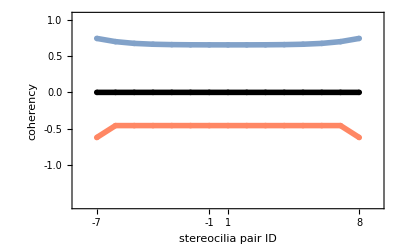

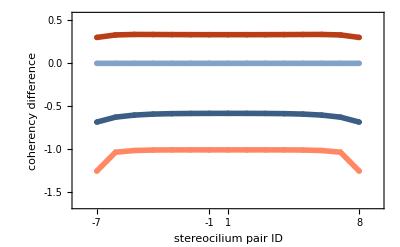

```mathematica
(*Figure C5C-C5D coherency differences vs stereocilium pairs *)

(*derivation of coherency vs stereocilium pairs*)
coherlowfreqelas0pairs[kk_]:=coherc2[16,kk,kk+1]/.{w->(2*Pi*10^2),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL};
coherhighfreqelas0pairs[kk_]:=coherc2[16,kk,kk+1]/.{w->(2*Pi*10^6),kA1->kA,lA1->lA,kL1->0*kL,lL1->lL};

coherlowfreqxyelas0pairs=Table[{i,coherlowfreqelas0pairs[i]},{i,-7,7}];
coherhighfreqxyelas0pairs=Table[{i,coherhighfreqelas0pairs[i]},{i,-7,7}];

(*plot settings*)
plotstylecoh3={{Thickness->0.01, RGBColor[255/255, 135/255, 100/255]},{Thickness->0.01, RGBColor[130/255, 162/255, 201/255]},{Thickness->0.01, Black}};
plotstylecoh4={{Thickness->0.01, RGBColor[255/255, 135/255, 100/255]},{Thickness->0.01, RGBColor[130/255, 162/255, 201/255]},{Thickness->0.01,RGBColor[185/255, 62/255, 23/255]},{Thickness->0.01, RGBColor[60/255, 93/255, 132/255]},{Thickness->0.01, Black}};

Remove[XTicks,YTicks]
pady=80;
padx=60;
pad2=30;

XTicks={{-7,-7,{0,TickLength1}},{-6,Null,{0,0.02}},{-5,Null,{0,0.02}},{-4,Null,{0,0.02}},{-3,Null,{0,0.02}},{-2,Null,{0,0.02}},{-1,-1,{0,TickLength1}},{0,1,{0,0.02}},{1,Null,{0,TickLength2}},{2,Null,{0,0.02}},{3,Null,{0,0.02}},{4,Null,{0,0.02}},{5,Null,{0,0.02}},{6,Null,{0,0.02}},{7,8,{0,0.03}}};
YTicks={{0.0,"0.0",{0,0.03}},{0.5,0.5,{0,0.03}},{-0.5,-0.5,{0,0.03}},{1.0,"1.0",{0,0.03}},{-1.0,"-1.0",{0,0.03}},{0.1,Null,{0,0.02}},{0.2,Null,{0,0.02}},{0.3,Null,{0,0.02}},{0.4,Null,{0,0.02}},{0.6,Null,{0,0.02}},{0.7,Null,{0,0.02}},{0.8,Null,{0,0.02}},{0.9,Null,{0,0.02}},{-0.1,Null,{0,0.02}},{-0.2,Null,{0,0.02}},{-0.3,Null,{0,0.02}},{-0.4,Null,{0,0.02}},{-0.6,Null,{0,0.02}},{-0.7,Null,{0,0.02}},{-0.8,Null,{0,0.02}},{-0.9,Null,{0,0.02}}};

framelabelscoherdiff1={{"coherency difference",None},{"stereocilium pair ID",None}};

plotrangecoherlowfreq={{-8,8},{-1.55,1.05}};

(*plot*)
ListPlot[{coherlowfreqxyelas0pairs,coherhighfreqxyelas0pairs,coherlowfreqxyall0pairs},Joined->True,PlotMarkers->plotmarkers,PlotRange->plotrangecoherlowfreq,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},
PlotStyle->plotstylecoh3, Background->White,Axes->{False,False},Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameLabel->framelabelslowfreq,FrameTicks -> {{YTicks, None}, {XTicks, None}}](*,FrameLabel->framelabels*)

(*derivation of coherency difference using previosly calculated values*)
coherlowfreqxyvisc0pairsdiff=Table[0,{coherlowfreqxyall0pairs},{2}];
coherhighfreqxyvisc0pairsdiff=Table[0,{coherlowfreqxyall0pairs},{2}];
For[kk=1,kk<=Length[coherlowfreqxyall0pairs],kk++,

coherlowfreqxyvisc0pairsdiff[[kk]][[1]]=coherlowfreqxyvisc0pairs[[kk]][[1]];
coherlowfreqxyvisc0pairsdiff[[kk]][[2]]=coherlowfreqxyvisc0pairs[[kk]][[2]]-coherlowfreqxypairs[[kk]][[2]];

coherhighfreqxyvisc0pairsdiff[[kk]][[1]]=coherhighfreqxyvisc0pairs[[kk]][[1]];
coherhighfreqxyvisc0pairsdiff[[kk]][[2]]=coherhighfreqxyvisc0pairs[[kk]][[2]]-coherhighfreqxypairs[[kk]][[2]];

]

coherlowfreqxyelas0pairsdiff=Table[0,{coherlowfreqxyall0pairs},{2}];
coherhighfreqxyelas0pairsdiff=Table[0,{coherlowfreqxyall0pairs},{2}];
For[kk=1,kk<=Length[coherlowfreqxyall0pairs],kk++,

coherlowfreqxyelas0pairsdiff[[kk]][[1]]=coherlowfreqxyelas0pairs[[kk]][[1]];
coherlowfreqxyelas0pairsdiff[[kk]][[2]]=coherlowfreqxyelas0pairs[[kk]][[2]]-coherlowfreqxypairs[[kk]][[2]];

coherhighfreqxyelas0pairsdiff[[kk]][[1]]=coherhighfreqxyelas0pairs[[kk]][[1]];
coherhighfreqxyelas0pairsdiff[[kk]][[2]]=coherhighfreqxyelas0pairs[[kk]][[2]]-coherhighfreqxypairs[[kk]][[2]];

]

(*plot settings*)
plotrangecoherlowfreq={{-8,8},{-1.65,0.55}};
YTicks={{0.0,"0.0",{0,0.03}},{0.5,0.5,{0,0.03}},{-0.5,-0.5,{0,0.03}},{1.0,"1.0",{0,0.03}},{-1.0,"-1.0",{0,0.03}},{0.1,Null,{0,0.02}},{0.2,Null,{0,0.02}},{0.3,Null,{0,0.02}},{0.4,Null,{0,0.02}},{0.6,Null,{0,0.02}},{0.7,Null,{0,0.02}},{0.8,Null,{0,0.02}},{0.9,Null,{0,0.02}},{-0.1,Null,{0,0.02}},{-0.2,Null,{0,0.02}},{-0.3,Null,{0,0.02}},{-0.4,Null,{0,0.02}},{-0.6,Null,{0,0.02}},{-0.7,Null,{0,0.02}},{-0.8,Null,{0,0.02}},{-0.9,Null,{0,0.02}},{-1.1,Null,{0,0.02}},{-1.2,Null,{0,0.02}},{-1.3,Null,{0,0.02}},{-1.4,Null,{0,0.02}},{-1.5,"-1.5",{0,0.03}}};

(*plot*)
ListPlot[{coherlowfreqxyelas0pairsdiff,coherhighfreqxyelas0pairsdiff,coherlowfreqxyvisc0pairsdiff,coherhighfreqxyvisc0pairsdiff},Joined->True,PlotMarkers->plotmarkers,PlotRange->plotrangecoherlowfreq,ImagePadding -> {{pady, pad2}, {padx, pad2}},ImageSize->400,LabelStyle->{FontSize->fntsize},
PlotStyle->plotstylecoh4, Background->White,Frame->{True,True,True,True},FrameStyle->Directive[Black,Thick],FrameLabel->framelabelscoherdiff1,FrameTicks -> {{YTicks, None}, {XTicks, None}},Axes->{False,False}]
```